Computational Journey of Quantum Mechanics | Amir H. Ebrahimnezhad | Advisor: Prf. Ebrahim | University of Tehran

# Quantum Mechanics Principles & Foundations

## Overview

Quantum Mechanics stands as humanity’s most profound and precisely verified theory of nature’s fundamental behavior. Unlike classical physics that governs our everyday experience, quantum mechanics reveals a reality that operates by starkly different rules at the atomic and subatomic scales. This foundational theory rests upon the elegant mathematical framework of linear algebra, offering a relatively accessible mathematical entry point compared to other advanced physical theories like Quantum Field Theory or General Relativity.

Despite its mathematical clarity, quantum mechanics presents conceptual challenges that have confounded even its founding figures. As Richard Feynman famously remarked, “I think I can safely say that nobody understands quantum mechanics.” This paradox—a theory of unparalleled predictive success that defies intuitive understanding—represents one of the most fascinating aspects of modern physics.

This notebook serves as an introduction to the historical development, mathematical foundations, and core principles of quantum mechanics. We will explore the critical experiments that revealed the quantum nature of reality, examine the mathematical formalism that describes quantum systems, and investigate the interpretational challenges that continue to engage physicists and philosophers alike. Through visualizations and conceptual explanations, we aim to build an intuitive foundation for understanding this revolutionary framework, preparing the groundwork for more advanced explorations in subsequent notebooks.

## The Quantum Revolution: History

## The Crisis in Classical Physics (Late 19th Century)

In the second half of the nineteenth century it seemed that the laws of classical mechanics, developed by works of Newton, Lagrange, Hamilton, Jacobi and Poincare, in addition with the Maxwell theory of electromagnetic phenomena completely describe the reality. Despite that we gradually understood that for explaining some particular phenomenas we must reduce to a new kind of mechanics, since classical mechanics would not tackle them at ease. 

Before developing any new ground breaking theory of any sort, a wise scientist would not ruin the palace of older theories, but instead, they would try to a process known as ad-hoc. Adding small adjustments to the current theory in order to make it apply to the current problems. This of course happened before the development of quantum mechanics.

By the early 20th century, there were little to no problem that was challenging by the rich framework of Classical Mechanics (which back then wouldn’t be called classical). But surely some types of problems emerged, making it obvious that we’re facing a new world. The world of modern physics.

## Black Body Radiation and Planck’s Quantum Hypothesis

A blackbody is an idealized physical object that perfectly absorbs and emits electromagnetic radiation. The radiation it emits is called blackbody radiation, and its spectral distribution depends only on the temperature. We here aim to calculate the spectral energy density --the energy per unit volume per unit frequency interval at temperature .

### Classical Derivation

#### Counting Modes

We imagine a cubical  cavity of volume , with perfectly conducting walls. Electromagnetic waves inside the cavity form standing waves. The boundary conditions require the wave vector components to be of below:

```mathematica
V = L^3;
k[nx_,ny_,nz_]:=π/L{nx,ny,nz}
```

The number of modes in wave-vector space within a spherical shell of radius  and thickness  is given by:

```mathematica
dN =2 V/(2π)^3 4π (k^2)dk
```

(dk k^2 L^3)/π^2

The factor 2 accounts for the polarization states of electromagnetic waves. Now the frequency and wave vector are related as following:

```mathematica
dk = 2 π/c dν;
```

```mathematica
dN = dN /. k-> (2π)/c ν
```

(8 dν L^3 π ν^2)/c^3

This gives us the number of modes per unit volume per frequency:

```mathematica
dN/(V dν)
```

(8 π ν^2)/c^3

#### Equipartition of Energy

From classical statistical mechanics (equipartition theorem), each mode has average energy:

```mathematica
averageEnergy = kb T;
```

So the spectral energy density (energy per unit volume per unit frequency):

```mathematica
u[ν_,T_]:=(8π ν^2)/c^3 kb T;
```

#### Ultraviolet Catastrophe

As , . That is, the total energy diverges.

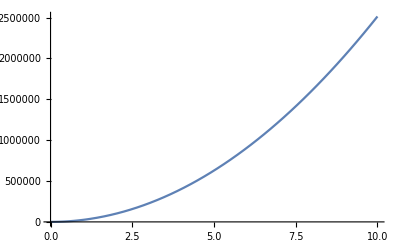

```mathematica
testT = 1000;
c=1;
kb=1;
Plot[u[x,testT], {x,0,10}]
Clear[c, kb];
```

```mathematica
Integrate[u[x,testT],{x,0,Infinity}]
```

Integrate::idiv: Integral of (8000 kb π x^2)/c^3 does not converge on {0,∞}.

∫_0^∞ (8000 kb π x^2)/c^3 ⅆx

Which violets energy conservation and contradicts experimental results... Classical physics breaks down.

### Quantum Derivation

In his attempts to derive the law for the spectral distribution of energy density of a body which is able to absorb all the radiant energy falling upon it, Planck was led to assume that the walls of such a body consist of harmonic oscillators, which exchange energy with the electromagnetic field inside the body only via integer multiples of a fundamental quantity . 

At this stage, to be consistent with another law that had been derived in a thermodynamical way and has and was hence of universal validity, the quantity  turned out to be proportional to the frequency of the radiation field, , and a new constant of nature, , with dimension [energy] [time] and since then called the Planck constant, was introduced for the first time. These problems are part of the general theory of heat radiation (Planck 1991).

#### Same Mode Counting

We use the same density of modes

```mathematica
dN/(V dν)
```

(8 π ν^2)/c^3

#### Quantum Energy Distribution

Now, instead of equipartition, each mode is a quantum harmonic oscillator with discrete energy levels:

```mathematica
e[n_, ν_]:=h n ν
```

The average energy per mode is given by the Boltzmann weighted average:

```mathematica
Clear[averageEnergy];
averageEnergy[ν_,T_]:=(h ν)/(ⅇ^(h ν/kb T)-1)
```

```mathematica
averageEnergy[ν,T]
```

(h ν)/(-1+ⅇ^((h T ν)/kb))

Note: This is the Bose-Einstein occupation number times the quantum energy. So, the energy density becomes:

```mathematica
quantumU[ν_, T_]:=(8 π ν^2)/c^3 averageEnergy[ν, T]
```

#### Planck’s Law

The final result  is known as the Planck distribution, and it matches experimental results perfectly.

```mathematica
quantumU[ν,T]
```

(8 h π ν^3)/(c^3 (-1+ⅇ^((h T ν)/kb)))

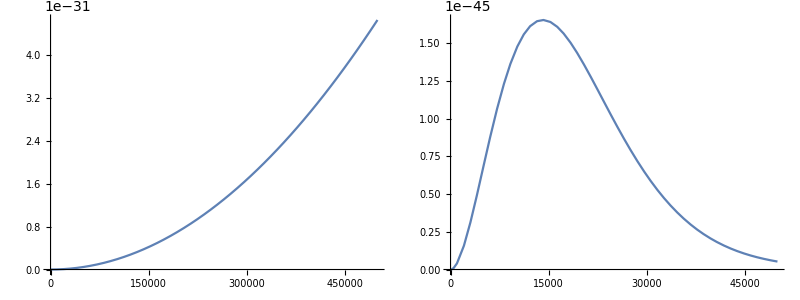

```mathematica
kb=10^-23;
c=3 10^8;
h=10^-32;
testT=200000;
Grid[{{Plot[u[x,testT],{x,0.1,500000} ],
Plot[quantumU[x,testT],{x,0.1,50000}]}}]
Clear[kb,c,testT,h]
```

## Einstein’s Explanation of the Photoelectric Effect

The photoelectric effect was a pivotal phenomenon that helped establish quantum theory. While Heinrich Hertz first observed the effect in 1887, it was Albert Einstein who provided the revolutionary explanation in 1905 that would earn him the Nobel Prize in Physics in 1921.

### The Classical Paradox

Before Einstein, physicists attempted to explain the photoelectric effect using classical electromagnetic theory. According to classical physics, light is a wave that carries energy continuously. When light shines on a metal surface, this energy should gradually accumulate in the electrons until they gain enough energy to escape the metal, regardless of the light’s frequency. Classical theory predicted:

Increasing light intensity should increase the energy of emitted electrons

All frequencies of light should be able to eject electrons, given sufficient intensity

There should be a delay between illumination and electron emission at low intensities

However, experiments revealed bewildering results:

The energy of emitted electrons depends only on the frequency of light, not its intensity

Below a certain threshold frequency, no electrons are emitted regardless of intensity

Electron emission occurs with no measurable delay, even at very low intensities

Let’s visualize the experimental setup and results using Mathematica:

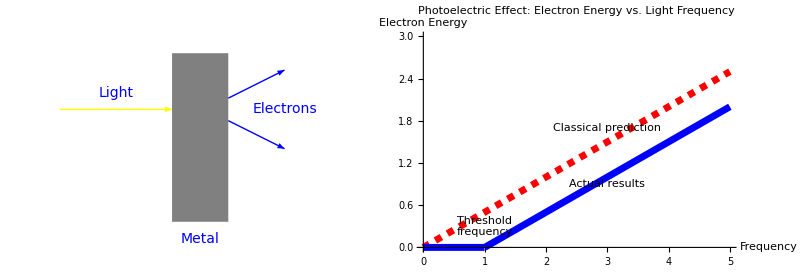

```mathematica
(* Create a simple diagram of the photoelectric effect experiment *)
photoelectricSetup = Graphics[{
   (* Metal plate *)
   Gray, Rectangle[{0, 0}, {1, 3}],
   (* Light beam *)
   Yellow, Arrow[{{-2, 2}, {0, 2}}],
   (* Ejected electrons *)
   Blue, Arrow[{{1, 2.2}, {2, 2.7}}],
   Blue, Arrow[{{1, 1.8}, {2, 1.3}}],
   (* Labels *)
   Text[Style["Light", 14], {-1, 2.3}],
   Text[Style["Metal", 14], {0.5, -0.3}],
   Text[Style["Electrons", 14], {2, 2}]
   }, PlotRange -> {{-2.5, 2.5}, {-0.5, 3.5}}, ImageSize -> 400];

(* Show the experimental results - Energy vs Frequency *)
classicalPrediction = Plot[0.5*f, {f, 0, 5}, 
   PlotStyle -> {Red, Dashed, Thickness[0.01]}, 
   PlotRange -> {{0, 5}, {0, 3}}];
   
quantumResult = Plot[If[f > 1, 0.5*(f - 1), 0], {f, 0, 5}, 
   PlotStyle -> {Blue, Thickness[0.01]}, 
   PlotRange -> {{0, 5}, {0, 3}}];
   
photoelectricPlot = Show[classicalPrediction, quantumResult, 
   PlotLabel -> "Photoelectric Effect: Electron Energy vs. Light Frequency", 
   AxesLabel -> {"Frequency", "Electron Energy"}, 
   Epilog -> {Text["Classical prediction", {3, 1.7}], 
       Text["Actual results", {3, 0.9}], 
       Text["Threshold\nfrequency", {1, 0.3}]},
   ImageSize -> 500];

GraphicsRow[{photoelectricSetup, photoelectricPlot}, Spacings -> 30]
```

### Einstein’s Quantum Solution

Einstein proposed a radical explanation: light consists of discrete packets of energy called photons (though he called them “light quanta” at the time). Each photon carries an energy proportional to its frequency:

where:

is the energy of a single photon

is Planck's constant (approximately  J·s)

is the frequency of the light

Einstein’s model explained the observations perfectly:

A single photon can eject at most one electron

Intensity affects the number of photons, not their individual energy

Electrons are ejected only if photon energy exceeds the metal’s work function

The maximum kinetic energy of ejected electrons follows a simple equation:
.
Where  is the work function of the metal (minimum energy needed to remove an electron). Let’s simulate the photoelectric effect with Mathematica:

```mathematica
(* Define constants *)
h = 6.626*10^-34; (* Planck's constant in J·s *)
eV = 1.602*10^-19; (* conversion from eV to Joules *)

(* Function to calculate maximum kinetic energy *)
maxKineticEnergy[frequency_, workFunction_] := Max[0, h*frequency - workFunction];

(* Interactive demonstration of the photoelectric effect *)
Manipulate[
  Module[{maxEnergy, photonEnergy},
    photonEnergy = h*frequency;
    maxEnergy = maxKineticEnergy[frequency, workFunction];
    
    Column[{
      (* Visualization *)
      Graphics[{
        (* Metal surface *)
        Gray, Rectangle[{-5, -2}, {0, 2}],
        
        (* Incoming photons *)
        Dynamic@Table[
          {Yellow, Disk[{-7 + Mod[t + i/3, 7], 0}, 0.2]},
          {i, 1, intensity}
        ],
        
        (* Electrons ejected (only if above threshold) *)
        If[photonEnergy > workFunction,
          Dynamic@Table[
            {Blue, Disk[{0.5 + Mod[t + i/5, 4], 0}, 0.15]},
            {i, 1, Min[intensity, 5]}
          ],
          {}
        ],
        
        (* Labels *)
        Text[Style["Metal", 14], {-2.5, 0}],
        Text[Style["Photons", 14], {-7, 1}],
        If[photonEnergy > workFunction,
          Text[Style["Electrons", 14], {2, 1}],
          {}
        ],
        
        (* Energy indicators *)
        Text[Style["Photon Energy: " <> ToString[Round[photonEnergy/eV, 0.01]] <> " eV", 12], {-6, -1.5}],
        Text[Style["Work Function: " <> ToString[Round[workFunction/eV, 0.01]] <> " eV", 12], {-2.5, -1.5}],
        If[photonEnergy > workFunction,
          Text[Style["Electron Energy: " <> ToString[Round[maxEnergy/eV, 0.01]] <> " eV", 12], {2, -1.5}],
          Text[Style["No electrons ejected", Red, 12], {2, -1.5}]
        ]
      }, PlotRange -> {{-8, 5}, {-2, 2}}, ImageSize -> 500],
      
      (* Energy diagram *)
      Plot[{workFunction, If[x >= frequency, workFunction, Infinity]}, {x, 0, 2*frequency},
        Filling -> {1 -> Bottom},
        FillingStyle -> LightGray,
        PlotStyle -> {{Gray, Thickness[0.01]}, {Red, Thickness[0.01]}},
        PlotRange -> {{0, 2*frequency}, {0, 1.5*photonEnergy}},
        AxesLabel -> {"Frequency", "Energy"},
        Epilog -> {
          Line[{{frequency, 0}, {frequency, photonEnergy}}],
          Text["Threshold", {frequency, photonEnergy/4}],
          If[photonEnergy > workFunction,
            {Blue, Arrow[{{frequency + frequency/10, workFunction}, {frequency + frequency/5, workFunction + maxEnergy}}],
             Text["Electron\nKinetic Energy", {frequency + frequency/4, workFunction + maxEnergy/2}]},
            {}
          ]
        }
      ]
    }]
  ],
  {{frequency, 5*10^14, "Light Frequency (Hz)"}, 1*10^14, 10*10^14, 0.1*10^14},
  {{workFunction, 3.5*10^-19, "Work Function (J)"}, 1*10^-19, 5*10^-19, 0.1*10^-19},
  {{intensity, 3, "Light Intensity"}, 1, 10, 1},
  {{t, 0, ""}, 0, 10, 0.1, AnimationRate -> 1, AnimationRunning -> True, ControlType -> None}
]
```

General::prng: Value of option PlotRange -> {{0,1000000000000000},{0,7.5×10^14 h}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Let’s calculate the wavelength threshold for various metals:

Metal | Work Function (eV) | Threshold Wavelength (nm) | Visible Light?
Sodium | 2.28 | 544.2 | Yes
Aluminum | 4.08 | 304.1 | No
Copper | 4.7 | 264. | No
Silver | 4.26 | 291.3 | No
Gold | 5.1 | 243.3 | No
Platinum | 6.35 | 195.4 | No

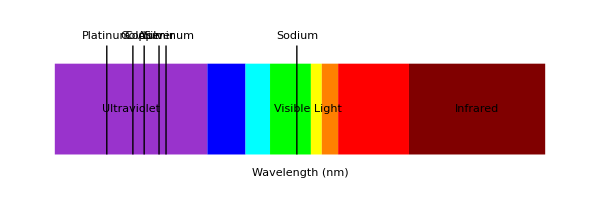

```mathematica
(* Work functions for common metals in electron volts *)
workFunctions = {
  {"Sodium", 2.28},
  {"Aluminum", 4.08},
  {"Copper", 4.70},
  {"Silver", 4.26},
  {"Gold", 5.10},
  {"Platinum", 6.35}
};

(* Calculate threshold wavelength *)
thresholdWavelength[workFunctionEV_] := (h*3*10^8)/(workFunctionEV*eV);

(* Create a table of results *)
Grid[
  Join[
    {{"Metal", "Work Function (eV)", "Threshold Wavelength (nm)", "Visible Light?"}},
    Table[
      With[{metal = wf[[1]], workFunction = wf[[2]], 
            wavelength = thresholdWavelength[wf[[2]]]*10^9},
        {metal, workFunction, Round[wavelength, 0.1], 
         If[380 <= wavelength <= 750, "Yes", "No"]}
      ],
      {wf, workFunctions}
    ]
  ],
  Frame -> All,
  Background -> {None, {LightYellow}}
]

(* Visualize the threshold wavelengths on the electromagnetic spectrum *)
spectrumColors = {
  {100, 380, RGBColor[0.6, 0.2, 0.8]}, (* ultraviolet *)
  {380, 450, Blue},                    (* violet *)
  {450, 495, Cyan},                    (* blue *)
  {495, 570, Green},                   (* green *)
  {570, 590, Yellow},                  (* yellow *)
  {590, 620, Orange},                  (* orange *)
  {620, 750, Red},                     (* red *)
  {750, 1000, RGBColor[0.5, 0, 0]}     (* infrared *)
};


spectrumBands=Table[{color[[3]],Rectangle[{color[[1]],0},{color[[2]],1}]},{color,spectrumColors}];

Graphics[{
  (* Draw spectrum bands *)
spectrumBands,
  
  (* Draw threshold markers *)
  Table[{Black, Line[{{thresholdWavelength[wf[[2]]]*10^9, 0}, 
          {thresholdWavelength[wf[[2]]]*10^9, 1.2}}],
         Text[wf[[1]], {thresholdWavelength[wf[[2]]]*10^9, 1.3}]},
    {wf, workFunctions}],
  
  (* Labels *)
  Text["Ultraviolet", {240, 0.5}],
  Text["Visible Light", {565, 0.5}],
  Text["Infrared", {875, 0.5}],
  Text["Wavelength (nm)", {550, -0.2}]
},
  PlotRange -> {{100, 1000}, {-0.3, 1.5}},
  ImageSize -> 600,
  AspectRatio -> 1/3
]
```

## The Bohr Model of the Atom

Niels Bohr’s atomic model, proposed in 1913, marked a critical transition between classical physics and the emerging quantum theory. While now superseded by more sophisticated quantum mechanical models, the Bohr model remains valuable as a conceptual stepping stone that successfully explained the hydrogen spectrum and introduced key quantum concepts.

### Historical Context

By the early 20th century, several key discoveries had undermined the classical understanding of atoms:

J.J. Thomson’s discovery of the electron (1897)

Ernest Rutherford’s gold foil experiment (1911), revealing a compact, positive nucleus

The precise, discrete spectral lines emitted by excited atoms

Rutherford proposed a “planetary model” with electrons orbiting the nucleus like planets around the sun. However, this model faced a devastating theoretical problem: according to classical electromagnetic theory, orbiting electrons should continuously emit radiation, spiral into the nucleus, and collapse the atom in microseconds.

### Bohr’s Revolutionary Postulates

Niels Bohr resolved this paradox by introducing radical assumptions that broke with classical physics :

Quantized orbits: Electrons can only occupy specific discrete orbits where the angular momentum is quantized (equal to an integer multiple of ħ = h/2π)

Stationary states: Electrons in these allowed orbits do not radiate energy despite their acceleration

Quantum jumps: Electrons change energy only by "jumping" between allowed energy levels, absorbing or emitting photons with energy equal to the difference between levels

Let’s implement the Bohr model in Mathematica:

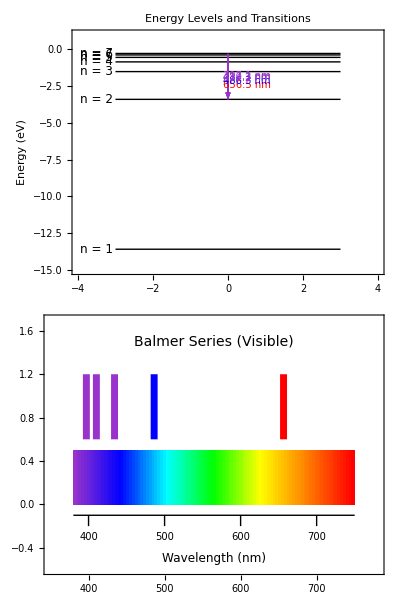

```mathematica
(*Constants*)
m=9.11*10^-31;             (*electron mass in kg*)
e=1.602*10^-19;            (*elementary charge in C*)
ϵ0=8.85*10^-12;   (*vacuum permittivity in F/m*)
h=6.626*10^-34;            (*Planck's constant in J·s*)
c=3*10^8;                  (*speed of light in m/s*)

(*Energy levels according to Bohr model for hydrogen*)
energyLevel[n_]:=-13.6/n^2;  (*in eV*)

(*Bohr radius for hydrogen-like atoms*)
bohrRadius[n_,Z_]:=0.0529*n^2/Z;  (*in nm*)

(*Create visualization of Bohr's model*)
bohrModelViz=Manipulate[
Module[
{radius,nucleusSize=0.01,electronSize=0.05},
radius=bohrRadius[n,1];
Graphics[
{
(*Nucleus*)
{Red,Disk[{0,0},nucleusSize]},
(*Electron orbits*)
Evaluate[
Table[
{LightGray,Circle[{0,0},bohrRadius[i,1]]},{i,1,5}
]
],
(*Current orbit highlight*)
{Blue,Thick,Circle[{0,0},radius]},
(*Electron*)
{Blue,Disk[radius*{Cos[angle],Sin[angle]},electronSize]},
(*Labels*)
Text[Style["n = "<>ToString[n],14],{0,-1.5*radius}],
Text[Style["Energy = "<>ToString[Round[energyLevel[n],0.01]]<>" eV",14],{0,-1.8*radius}],
Text[Style["Nucleus (proton)",12],{0,0.3}],
Text[Style["Electron",12],1.2*radius*{Cos[angle],Sin[angle]}]},
PlotRange->{{-3,3},{-3,3}},
ImageSize->400,
Frame->True,
FrameLabel->{"Position (nm)","Position (nm)"},
PlotLabel->Style["Bohr Model of Hydrogen Atom",16]
]
],
{{n,1,"Principal Quantum Number"},1,5,1},
{{angle,0,""},0,2 Pi,0.01,ControlType->None,AnimationRate->0.5,AnimationRunning->True}];

(*Create visualization of emission spectrum*)
transitionEnergy[nf_,ni_]:=energyLevel[nf]-energyLevel[ni];
wavelength[nf_,ni_]:=1240/Abs[transitionEnergy[nf,ni]];  (*in nm*)

spectrumViz=Module[
{transitions,spectrumColors,balmerTransitions},
(*Calculate transitions to n=2 (Balmer series)*)
balmerTransitions=Table[{i,2,wavelength[i,2]},{i,3,7}];
(*Assign colors based on wavelength*)spectrumColors=Table[
With[{λ=transition[[3]]},
{transition[[1]],
(*initial state*)
transition[[2]],
(*final state*)λ,
(*wavelength*)
Which[
(*color assignment*)
380<=λ<=450,RGBColor[0.6,0.2,0.8],(*violet*)
450<λ<=495,Blue,(*blue*)
495<λ<=570,Green,(*green*)
570<λ<=590,Yellow,(*yellow*)
590<λ<=620,Orange,(*orange*)
620<λ<=750,Red,(*red*)
True,
Gray (*outside visible*)]}],
{transition,balmerTransitions}
];
Column[{(*Energy level diagram*)Graphics[{(*Energy levels*)Table[{Line[{{-3,energyLevel[i]},{3,energyLevel[i]}}],Text[Style["n = "<>ToString[i],12],{-3.5,energyLevel[i]}]},{i,1,7}],(*Transitions*)Map[With[{n1=#[[1]],n2=#[[2]],λ=#[[3]],color=#[[4]]},{color,Arrow[{{0,energyLevel[n1]},{0,energyLevel[n2]}}],Text[Style[ToString[Round[λ,0.1]]<>" nm",10],{0.5,(energyLevel[n1]+energyLevel[n2])/2}]}]&,spectrumColors]},PlotRange->{{-4,4},{-15,1}},Frame->True,FrameLabel->{None,"Energy (eV)"},ImageSize->400,PlotLabel->Style["Energy Levels and Transitions",14]],
(*Spectral lines*)
Graphics[{
(*Background gradient representing visible spectrum*)
Table[
{
Blend[
{RGBColor[0.6,0.2,0.8],Blue,Cyan,Green,Yellow,Orange,Red},i/99],
Rectangle[{380+i*(750-380)/100,0},{380+(i+1)*(750-380)/100,0.5}]},{i,0,99}],
(*Scale*)
Line[{{380,-0.1},{750,-0.1}}],
Table[{Line[{{λ,-0.1},{λ,-0.2}}],
Text[Style[ToString[λ],10],{λ,-0.3}]},{λ,400,700,100}],
(*Spectral lines*)
Map[With[{λ=#[[3]],color=#[[4]]},
If[380<=λ<=750,{color,Thickness[0.01],Line[{{λ,0.6},{λ,1.2}}]}]]&,spectrumColors],
(*Labels*)
Text[Style["Balmer Series (Visible)",14],{565,1.5}],
Text[Style["Wavelength (nm)",12],{565,-0.5}]},
PlotRange->{{350,780},{-0.6,1.7}},ImageSize->500,
AspectRatio->1/3,Frame->True
]}]];

(*Display visualizations*)
Column[{bohrModelViz,spectrumViz},Spacings->2]
```

### Mathematical Formulation

Bohr' s theory can be derived from a few fundamental principles . For hydrogen - like atoms with atomic number  :

1. The electrostatic force provides the centripetal force necessary for circular motion :
   
2. The angular momentum is quantized :
   
From these conditions, we can derive the allowed radii :

Where  nm is the Bohr radius .
The allowed energy levels are :

Let' s calculate these values and compare with experimental data :

```mathematica
(* Create a table of energy levels *)
levels = Table[{n, energyLevel[n]}, {n, 1, 10}];

(* Calculate transition energies and wavelengths *)
transitionTable = Flatten[Table[
  With[{λ = wavelength[ni, nf], series = Which[
    nf == 1, "Lyman",
    nf == 2, "Balmer",
    nf == 3, "Paschen",
    nf == 4, "Brackett",
    nf == 5, "Pfund",
    True, "Other"
  ]},
  {ni, nf, series, energyLevel[ni], energyLevel[nf], 
   transitionEnergy[ni, nf], λ, 
   If[380 <= λ <= 750, "Visible", "Not visible"]}
  ],
  {nf, 1, 5}, {ni, nf + 1, nf + 5}
], 1];

(* Display the transition table *)
Grid[
  Join[
    {{"Initial n", "Final n", "Series", "Initial E (eV)", "Final E (eV)", 
      "Transition E (eV)", "Wavelength (nm)", "Visibility"}},
    transitionTable
  ],
  Frame -> All,
  Background -> {None, {LightYellow}},
  Dividers -> {{2 -> Black}, {2 -> Black}}
]

(* Compare with experimental values *)
experimentalData = {
  (* Series, n, Theoretical λ (nm), Experimental λ (nm) *)
  {"Balmer", 3, wavelength[3, 2], 656.3},
  {"Balmer", 4, wavelength[4, 2], 486.1},
  {"Balmer", 5, wavelength[5, 2], 434.1},
  {"Balmer", 6, wavelength[6, 2], 410.2},
  {"Lyman", 2, wavelength[2, 1], 121.6},
  {"Lyman", 3, wavelength[3, 1], 102.6},
  {"Paschen", 4, wavelength[4, 3], 1875.0},
  {"Paschen", 5, wavelength[5, 3], 1282.0}
};

(* Calculate accuracy *)
accuracy = Map[{#[[1]], #[[2]], #[[3]], #[[4]], 
  Round[100 * (1 - Abs[#[[3]] - #[[4]]]/{{#[[4]]}}), 0.01]} &, 
  experimentalData];

(* Display comparison *)
Grid[
  Join[
    {{"Series", "Transition", "Bohr Model (nm)", "Experimental (nm)", "Accuracy (%)"}},
    accuracy
  ],
  Frame -> All
]
```

Initial n | Final n | Series | Initial E (eV) | Final E (eV) | Transition E (eV) | Wavelength (nm) | Visibility
2 | 1 | Lyman | -3.4 | -13.6 | 10.2 | 121.569 | Not visible
3 | 1 | Lyman | -1.51111 | -13.6 | 12.0889 | 102.574 | Not visible
4 | 1 | Lyman | -0.85 | -13.6 | 12.75 | 97.2549 | Not visible
5 | 1 | Lyman | -0.544 | -13.6 | 13.056 | 94.9755 | Not visible
6 | 1 | Lyman | -0.377778 | -13.6 | 13.2222 | 93.7815 | Not visible
3 | 2 | Balmer | -1.51111 | -3.4 | 1.88889 | 656.471 | Visible
4 | 2 | Balmer | -0.85 | -3.4 | 2.55 | 486.275 | Visible
5 | 2 | Balmer | -0.544 | -3.4 | 2.856 | 434.174 | Visible
6 | 2 | Balmer | -0.377778 | -3.4 | 3.02222 | 410.294 | Visible
7 | 2 | Balmer | -0.277551 | -3.4 | 3.12245 | 397.124 | Visible
4 | 3 | Paschen | -0.85 | -1.51111 | 0.661111 | 1875.63 | Not visible
5 | 3 | Paschen | -0.544 | -1.51111 | 0.967111 | 1282.17 | Not visible
6 | 3 | Paschen | -0.377778 | -1.51111 | 1.13333 | 1094.12 | Not visible
7 | 3 | Paschen | -0.277551 | -1.51111 | 1.23356 | 1005.22 | Not visible
8 | 3 | Paschen | -0.2125 | -1.51111 | 1.29861 | 954.866 | Not visible
5 | 4 | Brackett | -0.544 | -0.85 | 0.306 | 4052.29 | Not visible
6 | 4 | Brackett | -0.377778 | -0.85 | 0.472222 | 2625.88 | Not visible
7 | 4 | Brackett | -0.277551 | -0.85 | 0.572449 | 2166.13 | Not visible
8 | 4 | Brackett | -0.2125 | -0.85 | 0.6375 | 1945.1 | Not visible
9 | 4 | Brackett | -0.167901 | -0.85 | 0.682099 | 1817.92 | Not visible
6 | 5 | Pfund | -0.377778 | -0.544 | 0.166222 | 7459.89 | Not visible
7 | 5 | Pfund | -0.277551 | -0.544 | 0.266449 | 4653.8 | Not visible
8 | 5 | Pfund | -0.2125 | -0.544 | 0.3315 | 3740.57 | Not visible
9 | 5 | Pfund | -0.167901 | -0.544 | 0.376099 | 3297.01 | Not visible
10 | 5 | Pfund | -0.136 | -0.544 | 0.408 | 3039.22 | Not visible

Series | Transition | Bohr Model (nm) | Experimental (nm) | Accuracy (%)
Balmer | 3 | 656.471 | 656.3 | {{99.97}}
Balmer | 4 | 486.275 | 486.1 | {{99.96}}
Balmer | 5 | 434.174 | 434.1 | {{99.98}}
Balmer | 6 | 410.294 | 410.2 | {{99.98}}
Lyman | 2 | 121.569 | 121.6 | {{99.97}}
Lyman | 3 | 102.574 | 102.6 | {{99.97}}
Paschen | 4 | 1875.63 | 1875. | {{99.97}}
Paschen | 5 | 1282.17 | 1282. | {{99.99}}

### Successes and Limitations

The Bohr model was remarkably successful in:

1. Explaining the hydrogen emission spectrum with unprecedented accuracy
2. Predicting the Rydberg constant value from fundamental constants
3. Introducing quantization and discrete energy levels
4. Establishing a theoretical framework for atomic physics

However, the model had significant limitations:

1. Failed to explain spectra of atoms with more than one electron
2. Could not explain the fine structure of spectral lines
3. Used an ad hoc mixture of classical and quantum concepts
4. Did not explain why only certain orbits were allowed

Keep in mind that this is hardly correct but just for the matter of checking out differences we’ve used a more (fairly more) corrected version of the equations.

## Wave-Particle Duality:The Cornerstone of Quantum Theory

## De Broglie’s Matter Waves Hypothesis

In 1924, Louis de Broglie presented a revolutionary doctoral thesis that would forever change our understanding of quantum mechanics. His central hypothesis—that particles such as electrons possess wave properties—provided a conceptual breakthrough that unified the seemingly contradictory wave and particle aspects of light and matter.

### The Dual Nature of Light

By the early 1920s, physicists faced a profound puzzle: light exhibited both wave-like behaviors (interference, diffraction) and particle-like behaviors (photoelectric effect, Compton scattering). Einstein had shown that light waves could behave as particles (photons), but de Broglie made the daring intellectual leap in the opposite direction—proposing that particles traditionally thought of as corpuscular could exhibit wave-like properties.

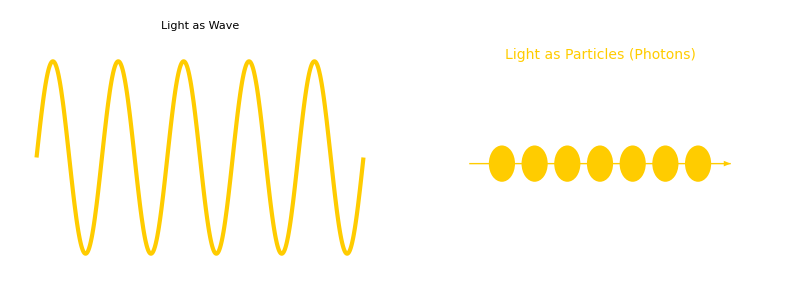
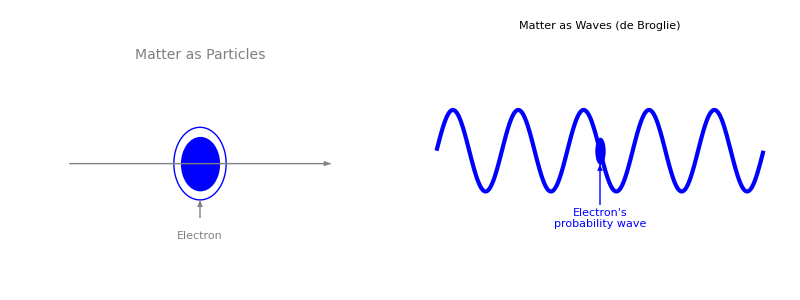
Wave-Particle Duality
-Graphics-

-Graphics-

```mathematica
(*Visualization of wave-particle duality*)
dualityViz=Column[{
(*Title*)
Text[Style["Wave-Particle Duality",Bold,16]],
(*Light behavior*)Grid[
{
{
(*Light as wave*)
Plot[Sin[5 x],{x,0,2 Pi},
PlotStyle->{Thickness[0.01],
RGBColor[1,0.8,0]},
PlotLabel->Style["Light as Wave",14],
Axes->False,
PlotRange->{{0,2 Pi},{-1.2,1.2}},
ImageSize->300],
(*Light as particles*)
Graphics[
{
(*Photon path*)
RGBColor[1,0.8,0],
Arrow[{{0,0},{4,0}}],
(*Photon particles*)
Table[{RGBColor[1,0.8,0],Disk[{x,0},0.2]},{x,0.5,3.5,0.5}],
(*Labels*)
Text[Style["Light as Particles (Photons)",14],{2,1.2}]},PlotRange->{{-0.5,4.5},{-1.2,1.5}},ImageSize->300]}}],
(*Spacer*)
Spacer[10],
(*De Broglie's hypothesis*)
Grid[{{
(*Matter as particles*)
Graphics[{
(*Electron*)
Blue,
Disk[{2,0},0.3],Circle[{2,0},0.4,{0,2Pi}],
(*Path*)
Gray,
Arrow[{{0,0},{4,0}}],
(*Labels*)
Text[Style["Matter as Particles",14],{2,1.2}],
Text["Electron",{2,-0.8}],Arrow[{{2,-0.6},{2,-0.4}}]},
PlotRange->{{-0.5,4.5},{-1.2,1.5}},ImageSize->300],
(*De Broglie's hypothesis:Matter as waves*)
Plot[0.3*Sin[5 x]+0.7,{x,0,2 Pi},
PlotStyle->{Thickness[0.01],Blue},
PlotLabel->Style["Matter as Waves\n(de Broglie)",14],
Axes->False,
PlotRange->{{0,2 Pi},{-0.2,1.5}},
Epilog->{Blue,Disk[{Pi,0.7},0.1],
Text["Electron's\nprobability wave",{Pi,0.2}],
Arrow[{{Pi,0.3},{Pi,0.6}}]},
ImageSize->300]}
}]}
]
```

### The de Broglie Wavelength

The central equation of de Broglie’s hypothesis relates the wavelength of a matter wave to the momentum of the particle:


Where:

is the de Broglie wavelength

is Planck’s constant ( J·s)

is the momentum of the particle

is the mass of the particle

v is the velocity of the particle

This elegant equation suggests that all matter has an associated wavelength that is inversely proportional to its momentum. Let’s explore this relationship with Mathematica:

```mathematica
(* Constants *)
h=6.626 10^-34;
massOfElectron=9.11 10^-31;
massOfProton= 1.673 10^-27;
massOfNeutron=1.675 10^-27;
eV=1.602 10^-19;

(*De Broglie wavelength function*)
deBroglieWavelength[mass_,velocity_]:=h/(mass*velocity);
deBroglieWavelengthEnergy[mass_,energy_]:=h/Sqrt[2*mass*energy];
```

```mathematica
(*Interactive demonstration of de Broglie wavelength*)
Manipulate[Module[{λ,p,v,particleMass},(*Set the particle mass based on selection*)particleMass=Which[particle=="Electron",massOfElectron,particle=="Proton",massOfProton,particle=="Neutron",massOfNeutron,particle=="Sodium atom",3.82*10^-26];
(*Calculate wavelength based on energy*)λ=deBroglieWavelengthEnergy[particleMass,energy*eV];
v=Sqrt[2*energy*eV/particleMass];
p=particleMass*v;
Column[{(*Display calculated values*)Grid[{{"Particle:",particle},{"Mass:",ToString[ScientificForm[particleMass]]<>" kg"},{"Energy:",ToString[energy]<>" eV"},{"Velocity:",ToString[ScientificForm[v/1000]]<>" km/s ("<>ToString[NumberForm[100*v/299792458,{3,2}]]<>"% of c)"},{"de Broglie wavelength:",ToString[NumberForm[λ*10^9,{4,8}]]<>" nm"}}],(*Visualization*)Graphics[{(*Particle representation*)Which[particle=="Electron",{Blue,Disk[{0,0},0.05]},particle=="Proton",{Red,Disk[{0,0},0.08]},particle=="Neutron",{Gray,Disk[{0,0},0.08]},particle=="Sodium atom",{Yellow,Disk[{0,0},0.12]}],(*Associated wave-scaled for visualization*)Blue,Thickness[0.005],Line[Table[{x,0.2*Sin[2*Pi*x/0.3]},{x,-2,2,0.01}]],(*Wavelength indicator*)Red,Arrow[{{-0.3,-0.15},{0,-0.15}}],Arrow[{{0,-0.15},{0.3,-0.15}}],Text["λ",{0,-0.25}],(*Context objects for scale reference*)Gray,Line[{{-2,-0.5},{2,-0.5}}],(*"surface"*)(*Scale references*)Which[λ>10^-9,{Text["Scale reference: Human hair (~100 μm)",{0,-0.7}]},λ>10^-10,{Text["Scale reference: Atom (~0.1 nm)",{0,-0.7}]},True,{Text["Scale reference: Nucleus (~1 fm)",{0,-0.7}]}]},PlotRange->{{-2,2},{-1,1}},ImageSize->400],(*Comparison with everyday objects*)Text[Style["Comparative Wavelengths:",Bold,12]],Grid[{{"Object","Typical de Broglie wavelength"},{"Electron in CRT","0.01 - 0.1 nm"},{"Thermal neutron","0.1 - 0.2 nm"},{"Baseball (40 m/s)","10^-34 m (undetectable)"},{"Human walking","10^-36 m (undetectable)"}},Frame->All]}]],{{particle,"Electron","Particle type"},{"Electron","Proton","Neutron","Sodium atom"}},{{energy,100,"Energy (eV)"},1,10000,1,Appearance->"Labeled"}]
```

### Experimental Confirmation

De Broglie' s hypothesis initially seemed like a mathematical curiosity with little experimental backing . However, in 1927, Clinton Davisson and Lester Germer at Bell Labs accidentally discovered electron diffraction while studying electron scattering from nickel crystals . Their experiment showed that electrons could indeed produce diffraction patterns—a phenomenon previously associated only with waves .
   
Let' s model the Davisson - Germer experiment :

```mathematica
(* Davisson-Germer experiment visualization *)
davisson = Module[{},
  Graphics[{
    (* Electron gun *)
    Gray, Rectangle[{-4, -0.5}, {-3, 0.5}],
    Black, Rectangle[{-3, -0.2}, {-2.5, 0.2}],
    
    (* Nickel crystal *)
    Gray, Polygon[{{-0.5, -1}, {0.5, -1}, {0.5, 1}, {-0.5, 1}}],
    
    (* Crystal lattice points *)
    Table[{Black, Disk[{-0.5 + 0.2*i, -1 + 0.2*j}, 0.03]}, 
          {i, 0, 5}, {j, 0, 10}],
    
    (* Detector *)
    Gray, Rectangle[{1.5, -0.8}, {2, 0.8}],
    
    (* Diffracted electrons *)
    Blue, Arrow[{{-2.5, 0}, {-0.5, 0}}],
    
    (* Diffraction pattern *)
    Blue, Arrow[{{0.5, 0.3}, {1.5, 0.6}}],
    Blue, Arrow[{{0.5, 0}, {1.5, 0}}],
    Blue, Arrow[{{0.5, -0.3}, {1.5, -0.6}}],
    
    (* Labels *)
    Text[Style["Electron Gun", 12], {-3.5, 1}],
    Text[Style["Nickel Crystal", 12], {0, 1.5}],
    Text[Style["Detector", 12], {1.75, 1.5}],
    Text[Style["Incident\nElectron Beam", 10], {-1.5, 0.3}],
    Text[Style["Diffracted\nElectrons", 10], {1, 0.8}]
  },
  PlotRange -> {{-4.5, 2.5}, {-1.5, 2}},
  ImageSize -> 500]
];

(* Diffraction pattern simulation *)
diffractionPattern = DensityPlot[
  Sum[Cos[5*((x - 0.5*i)^2 + (y - 0.5*j)^2)]^2, {i, -2, 2}, {j, -2, 2}],
  {x, -3, 3}, {y, -3, 3},
  ColorFunction -> "Rainbow",
  PlotPoints -> 100,
  PlotLabel -> Style["Electron Diffraction Pattern", 14],
  Frame -> True,
  FrameLabel -> {"Position", "Position"},
  ImageSize -> 400
];

(* Display both visualizations *)
Column[{davisson, diffractionPattern}]
```

-Graphics-

Another crucial confirmation came from G.P. Thomson (son of J.J. Thomson, who discovered the electron), who independently observed electron diffraction by passing electrons through thin metal foils. Ironically, J.J. Thomson had received the Nobel Prize for proving that electrons were particles, while his son later shared the Nobel Prize for proving electrons were also waves!

### Bohr Model Reinterpreted

De Broglie’s hypothesis provided a natural explanation for Bohr’s quantization conditions. He proposed that electrons in allowed Bohr orbits must form standing waves around the nucleus. For a wave to be stable (standing), its wavelength must fit the orbit circumference an integer number of times:

```mathematica
(*Standing wave visualization*)standingWaveViz=Manipulate[Module[{radius=1.0},Column[{Text[Style["De Broglie's Standing Wave Condition",Bold,14]],Graphics[{(*Nucleus*)Red,Disk[{0,0},0.1],(*Orbit*)Gray,Circle[{0,0},radius],(*Standing wave*)Blue,Thick,Line[Table[{radius*Cos[t],radius*Sin[t]+0.1*Sin[n*t]},{t,0,2*Pi,0.01}]],(*Labels*)Text[Style["n = "<>ToString[n],14],{0,-1.3}],Text[Style[ToString[n]<>" wavelengths fit around the orbit",12],{0,-1.5}],Text[Style["Nucleus",12],{0,0.3}],(*Wavelength indicator*)If[n>=1,{Red,Arrow[{{radius*Cos[0],radius*Sin[0]},{radius*Cos[2*Pi/n],radius*Sin[2*Pi/n]}}],Text["λ",{radius*Cos[Pi/n],radius*Sin[Pi/n]-0.2}]},{}]},PlotRange->{{-1.7,1.7},{-1.7,1.7}},ImageSize->400],Text[Style["Mathematical Relationship:",Bold,12]],Text["n * λ = 2π * r"],Text["For quantum number n = "<>ToString[n]<>", exactly "<>ToString[n]<>" wavelengths fit around the orbit circumference"]}]],{{n,3,"Quantum Number (n)"},1,10,1,Appearance->"Labeled"}];

(*Combination of Bohr model and de Broglie waves*)
deBroglieBohr=Column[{standingWaveViz,(*Explanation of how de Broglie resolved Bohr's ad hoc assumption*)Panel[Column[{Text[Style["How De Broglie's Hypothesis Explains Bohr's Quantization",Bold,14]],"",Text["Bohr's model required the arbitrary assumption that angular momentum is quantized:"],Text["mvr = nħ"],"",Text["De Broglie showed this follows naturally from the wave nature of electrons:"],Text["1. Electron wavelength: λ = h/mv"],Text["2. Standing wave condition: nλ = 2πr"],"",Text["Combining these equations:"],Text["n(h/mv) = 2πr"],Text["nh = 2πmvr"],Text["mvr = nh/2π = nħ"],"",Text[Style["This derives Bohr's quantization condition from more fundamental principles!",Bold,12]]}],ImageMargins->10]}]
```

How De Broglie's Hypothesis Explains Bohr's Quantization

Bohr's model required the arbitrary assumption that angular momentum is quantized:
mvr = nħ

De Broglie showed this follows naturally from the wave nature of electrons:
1. Electron wavelength: λ = h/mv
2. Standing wave condition: nλ = 2πr

Combining these equations:
n(h/mv) = 2πr
nh = 2πmvr
mvr = nh/2π = nħ

This derives Bohr's quantization condition from more fundamental principles!

### Beyond Atoms: Matter Waves in Modern Physics

De Broglie' s matter wave hypothesis extends far beyond the hydrogen atom . It applies to all matter, though the wavelengths for macroscopic objects are typically too small to detect . For subatomic particles, however, the wave nature becomes essential :

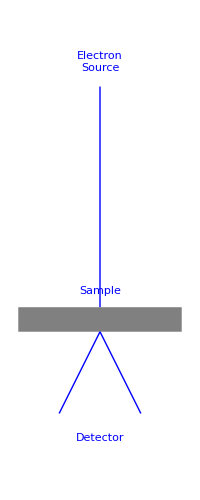
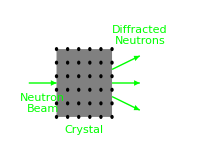
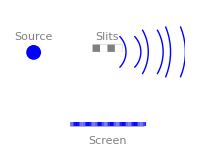
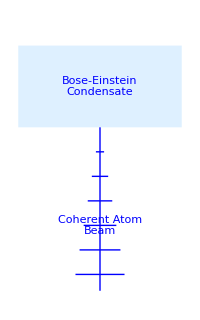
Object | de Broglie Wavelength | Object Size | Wave Effects?
Electron (1 eV) | 1.23 nm | 0.1 nm | Observable
Electron (100 keV) | 3.88 pm | 0.1 nm | Negligible
Neutron (thermal) |          26
1.47 × 10 nm | 0.1 nm | Observable
Helium atom (room temp) |          25
7.38 × 10 nm | 0.1 nm | Observable
Dust particle (1 μm) | 0.00 pm | 1 μm | Negligible
Baseball (40 m/s) |          -22
1.14 × 10 pm | 7.3 cm | Negligible
Applications of Matter Waves in Modern Physics
Electron Microscopy
-Graphics-
• Resolution limited by λ = h/mv
• 100 keV electrons: λ ≈ 4 pm
• Far better than optical microscopes | Neutron Diffraction
-Graphics-
• Thermal neutrons: λ ≈ 0.2 nm
• Penetrates materials deeply
• Sensitive to magnetic structure
Quantum Interference
-Graphics-
• Matter waves interfere with themselves
• Even single particles show interference
• Foundational to quantum mechanics | Modern Applications
• Electron Lithography
• Scanning Tunneling Microscopy
• Atom Interferometry
• Quantum Computing
• Neutron Scattering Analysis
• Atom Lasers
-Graphics-

```mathematica
(*Constants-make sure these are defined*)h=6.626*10^-34;    (*Planck's constant in J⋅s*)
massOfElectron=9.11*10^-31;    (*Mass of electron in kg*)
kB=1.38*10^-23;    (*Boltzmann constant*)
eV=1.602*10^-19;   (*Electron volt in Joules*)

(*De Broglie wavelength function if not already defined*)
deBroglieWavelength[mass_,velocity_]:=h/(mass*velocity);

(*Table of de Broglie wavelengths for various objects*)
wavelengthTable=Module[{objects,masses,velocities,wavelengths,wavelengthsText},objects={"Electron (1 eV)","Electron (100 keV)","Neutron (thermal)","Helium atom (room temp)","Dust particle (1 μm)","Baseball (40 m/s)"};
masses={massOfElectron,massOfElectron,1.675*10^-27,6.646*10^-27,10^-15,0.145};
velocities={Sqrt[2*eV/massOfElectron],(*1 eV electron*)Sqrt[2*100000*eV/massOfElectron],(*100 keV electron*)Sqrt[3*kB*293/1.675*10^-27],(*thermal neutron at room temp*)Sqrt[3*kB*293/6.646*10^-27],(*helium at room temp*)0.001,(*dust particle at 1 mm/s*)40                                        (*baseball at 40 m/s*)};
wavelengths=deBroglieWavelength[#1,#2]&@@@Transpose[{masses,velocities}];
(*Convert to appropriate units*)wavelengthsText=Map[If[#>10^-10,ToString[NumberForm[#*10^9,{4,2}]]<>" nm",ToString[NumberForm[#*10^12,{4,2}]]<>" pm"]&,wavelengths];
(*Compare to object size*)objectSizes={"0.1 nm","0.1 nm","0.1 nm","0.1 nm","1 μm","7.3 cm"};
(*Create comparison table*)Grid[Join[{{"Object","de Broglie Wavelength","Object Size","Wave Effects?"}},Transpose[{objects,wavelengthsText,objectSizes,Map[If[#>10^-11,"Observable","Negligible"]&,wavelengths]}]],Frame->All,Background->{None,{LightYellow}}]];

(*Applications of matter waves*)
matterWaveApplications=Column[{Text[Style["Applications of Matter Waves in Modern Physics",Bold,16]],Grid[{{(*Electron Microscopy*)Panel[Column[{Text[Style["Electron Microscopy",Bold,14]],Graphics[{(*Sample*)Gray,Rectangle[{0,0},{2,0.3}],(*Electron beam*)Blue,Line[{{1,3},{1,0.3}}],(*Scattered electrons*)Blue,Line[{{1,0},{0.5,-1}}],Blue,Line[{{1,0},{1.5,-1}}],(*Labels*)Text["Electron\nSource",{1,3.3}],Text["Sample",{1,0.5}],Text["Detector",{1,-1.3}]},PlotRange->{{0,2},{-1.5,3.5}},ImageSize->200],Text["• Resolution limited by λ = h/mv"],Text["• 100 keV electrons: λ ≈ 4 pm"],Text["• Far better than optical microscopes"]}]],(*Neutron Diffraction*)Panel[Column[{Text[Style["Neutron Diffraction",Bold,14]],Graphics[{(*Crystal*)Gray,Rectangle[{0.5,0.5},{1.5,1.5}],(*Atoms in crystal*)Table[{Black,Disk[{0.5+0.2*i,0.5+0.2*j},0.03]},{i,0,5},{j,0,5}],(*Neutron beam*)Green,Arrow[{{0,1},{0.5,1}}],(*Diffracted neutrons*)Green,Arrow[{{1.5,1.2},{2,1.4}}],Green,Arrow[{{1.5,1},{2,1}}],Green,Arrow[{{1.5,0.8},{2,0.6}}],(*Labels*)Text["Neutron\nBeam",{0.25,0.7}],Text["Crystal",{1,0.3}],Text["Diffracted\nNeutrons",{2,1.7}]},PlotRange->{{-0.2,2.2},{0,2}},ImageSize->200],Text["• Thermal neutrons: λ ≈ 0.2 nm"],Text["• Penetrates materials deeply"],Text["• Sensitive to magnetic structure"]}]]},{(*Quantum Interference*)Panel[Column[{Text[Style["Quantum Interference",Bold,14]],Graphics[{(*Double slit*)Gray,Rectangle[{0.8,0},{1.2,0.1}],White,Rectangle[{0.9,0},{1,0.1}],White,Rectangle[{1.1,0},{1.2,0.1}],(*Source*)Blue,Disk[{0,0},0.1],(*Waves*)Blue,Circle[{0.95,0},0.3,{-Pi/4,Pi/4}],Blue,Circle[{0.95,0},0.6,{-Pi/6,Pi/6}],Blue,Circle[{0.95,0},0.9,{-Pi/8,Pi/8}],Blue,Circle[{1.15,0},0.3,{-Pi/4,Pi/4}],Blue,Circle[{1.15,0},0.6,{-Pi/6,Pi/6}],Blue,Circle[{1.15,0},0.9,{-Pi/8,Pi/8}],(*Screen*)Gray,Line[{{0.5,-1},{1.5,-1}}],(*Interference pattern*)Table[{Blend[{White,Blue},0.5+0.5*Sin[20*x]^2],Rectangle[{0.5+x,-1},{0.5+x+0.02,-0.95}]},{x,0,1,0.02}],(*Labels*)Text["Source",{0,0.2}],Text["Slits",{1,0.2}],Text["Screen",{1,-1.2}]},PlotRange->{{-0.2,2},{-1.3,0.5}},ImageSize->200],Text["• Matter waves interfere with themselves"],Text["• Even single particles show interference"],Text["• Foundational to quantum mechanics"]}]],(*Practical Applications*)Panel[Column[{Text[Style["Modern Applications",Bold,14]],Text["• Electron Lithography"],Text["• Scanning Tunneling Microscopy"],Text["• Atom Interferometry"],Text["• Quantum Computing"],Text["• Neutron Scattering Analysis"],Text["• Atom Lasers"],Graphics[{(*Atom laser illustration*)LightBlue,Rectangle[{0,0},{2,1}],Blue,Line[{{1,0},{1,-2}}],Blue,Line[{{0.95,-0.3},{1.05,-0.3}}],Blue,Line[{{0.9,-0.6},{1.1,-0.6}}],Blue,Line[{{0.85,-0.9},{1.15,-0.9}}],Blue,Line[{{0.8,-1.2},{1.2,-1.2}}],Blue,Line[{{0.75,-1.5},{1.25,-1.5}}],Blue,Line[{{0.7,-1.8},{1.3,-1.8}}],Text["Bose-Einstein\nCondensate",{1,0.5}],Text["Coherent Atom\nBeam",{1,-1.2}]},PlotRange->{{0,2},{-2,1.2}},ImageSize->200]}]]}}]}];

(*Show all visualizations*)
Column[{wavelengthTable,matterWaveApplications}]
```

## The Double-Slit Experiment and Its Implications

### Historical Context

The double-slit experiment, first performed by Thomas Young in 1801, has evolved into one of the most profound demonstrations of quantum mechanical principles. Originally designed to investigate the wave nature of light, this deceptively simple experiment has become a cornerstone for understanding quantum behavior and the wave-particle duality that lies at the heart of quantum mechanics.

Let’s begin by exploring this experiment and its implications using Mathematica to visualize the concepts.

### Classical Wave Interference

Classical wave interference is a fundamental phenomenon that occurs when two or more waves overlap in space. When waves interfere, their amplitudes combine according to the superposition principle:

1. Constructive interference: When waves align in phase, their amplitudes add together, resulting in a larger amplitude.
2. Destructive interference: When waves are out of phase, their amplitudes subtract, potentially canceling each other out.

This phenomenon is crucial for understanding many physical systems, from water waves to electromagnetic radiation, and serves as a foundation for quantum mechanical wave behavior.

The mathematical representation of a one-dimensional wave can be expressed as:
   
Where:
   -  is the amplitude
   -  is the wave number (, where  is wavelength)
   -  is the angular frequency (, where  is frequency)
   -  is the phase constant

#### Visualization

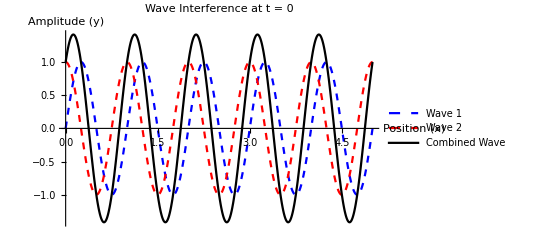

```mathematica
(* First, let's define a function for a traveling wave *)
travelingWave[x_, t_, amplitude_, wavelength_, frequency_, phase_] := 
  amplitude * Sin[2 Pi/wavelength * x - 2 Pi * frequency * t + phase]

(* Parameters for two waves *)
amplitude1 = 1;
amplitude2 = 1;
wavelength1 = 1;
wavelength2 = 1;
frequency1 = 1;
frequency2 = 1;
phase1 = 0;
phase2 = Pi/2; (* Phase difference of π/2 (quarter cycle) *)

(* Define the combined wave function *)
combinedWave[x_, t_] := 
  travelingWave[x, t, amplitude1, wavelength1, frequency1, phase1] + 
  travelingWave[x, t, amplitude2, wavelength2, frequency2, phase2]

(* VISUALIZATION *)
timeSlice = 0;
individualWavesPlot = Plot[{
  travelingWave[x, timeSlice, amplitude1, wavelength1, frequency1, phase1],
  travelingWave[x, timeSlice, amplitude2, wavelength2, frequency2, phase2],
  combinedWave[x, timeSlice]
  }, {x, 0, 5},
  PlotStyle -> {{Blue, Dashed}, {Red, Dashed}, {Black, Thick}},
  PlotLegends -> {"Wave 1", "Wave 2", "Combined Wave"},
  PlotLabel -> "Wave Interference at t = " <> ToString[timeSlice],
  AxesLabel -> {"Position (x)", "Amplitude (y)"}
]
```

#### Evolution

```mathematica
waveAnimation = Animate[
  Plot[{
    travelingWave[x, t, amplitude1, wavelength1, frequency1, phase1],
    travelingWave[x, t, amplitude2, wavelength2, frequency2, phase2],
    combinedWave[x, t]
    }, {x, 0, 5},
    PlotRange -> {{0, 5}, {-2.5, 2.5}},
    PlotStyle -> {{Blue, Dashed}, {Red, Dashed}, {Black, Thick}},
    PlotLegends -> {"Wave 1", "Wave 2", "Combined Wave"},
    PlotLabel -> "Wave Interference at t = " <> ToString[t],
    AxesLabel -> {"Position (x)", "Amplitude (y)"}
  ],
  {t, 0, 2, 0.05}
]
```

#### 2D Interference Pattern (like ripples on water)

```mathematica
wave2D[x_, y_, sourceX_, sourceY_, amplitude_, wavelength_, phase_] := 
  amplitude * Sin[2 Pi/wavelength * Sqrt[(x - sourceX)^2 + (y - sourceY)^2] + phase]

(* Two sources for circular waves *)
source1X = -2;
source1Y = 0;
source2X = 2;
source2Y = 0;

(* Combined 2D wave field *)
combinedWave2D[x_, y_] := 
  wave2D[x, y, source1X, source1Y, 1, 1, 0] + 
  wave2D[x, y, source2X, source2Y, 1, 1, 0]

(* Generate a 2D interference pattern *)
interferencePattern = DensityPlot[
  combinedWave2D[x, y], {x, -5, 5}, {y, -5, 5},
  PlotPoints -> 100,
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  PlotLabel -> "2D Wave Interference Pattern",
  FrameLabel -> {{"y position", None}, {"x position", None}}
]
```

-Graphics-

#### 3D Visualization

```mathematica
(* 4. 3D visualization of the interference pattern *)
interference3D = Plot3D[
  combinedWave2D[x, y], {x, -5, 5}, {y, -5, 5},
  PlotPoints -> 50,
  ColorFunction -> "TemperatureMap",
  PlotLabel -> "3D View of Wave Interference",
  AxesLabel -> {"x position", "y position", "amplitude"}
]
```

-Graphics3D-

#### Simple Interference Pattern of classical waves

-Graphics-

-Graphics-

-Graphics3D-

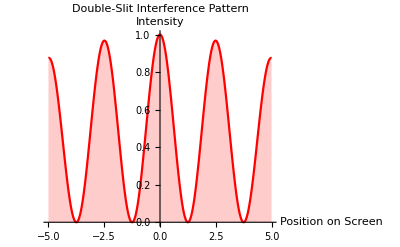

```mathematica
slitDistance = 2; (* Distance between slits *)
slitWidth = 0.2; (* Width of each slit *)
wavelength = 0.5; (* Wavelength of the wave *)
screenDistance = 10; (* Distance to the screen *)

(* Function to calculate intensity at a point on the screen *)
doubleSlit[y_] := Module[{d = slitDistance, a = slitWidth, λ = wavelength, L = screenDistance},
  (* Calculate the intensity using the double-slit formula *)
  (Sinc[Pi*a*y/(λ*L)]^2) * (Cos[Pi*d*y/(λ*L)]^2)
]

(* Plot the double-slit interference pattern intensity *)
doubleSitPattern = Plot[doubleSlit[y], {y, -5, 5},
  PlotRange -> All,
  PlotStyle -> Red,
  PlotLabel -> "Double-Slit Interference Pattern",
  AxesLabel -> {"Position on Screen", "Intensity"},
  Filling -> Axis
];

(* 5. Effect of changing phase difference *)
phaseEffectAnimation = Manipulate[
  Plot[{
    travelingWave[x, 0, 1, 1, 1, 0],
    travelingWave[x, 0, 1, 1, 1, phaseDiff],
    travelingWave[x, 0, 1, 1, 1, 0] + travelingWave[x, 0, 1, 1, 1, phaseDiff]
    }, {x, 0, 5},
    PlotRange -> {{0, 5}, {-2.5, 2.5}},
    PlotStyle -> {{Blue, Dashed}, {Red, Dashed}, {Black, Thick}},
    PlotLegends -> {"Wave 1", "Wave 2", "Combined Wave"},
    PlotLabel -> "Effect of Phase Difference = " <> ToString[N[phaseDiff/Pi]] <> "π",
    AxesLabel -> {"Position (x)", "Amplitude (y)"}
  ],
  {{phaseDiff, 0, "Phase Difference"}, 0, 2Pi, Pi/8}
];

(* Display the visualizations *)
individualWavesPlot
waveAnimation
interferencePattern
interference3D
doubleSitPattern 
phaseEffectAnimation
```

### Quantum Double-Slit: Particles Behaving as Waves

The double-slit experiment with quantum particles (electrons, photons, etc.) represents one of the most profound demonstrations of quantum mechanical behavior.

Key aspects:
1. Wave-Particle Duality: Quantum particles exhibit both wave-like and particle-like properties.
2. Superposition: Before measurement, particles exist in superposition states representing all possible paths.
3. Measurement Effect: The act of observation collapses the wavefunction and alters the experimental outcome.

Historical Significance:
Richard Feynman called this experiment “a phenomenon which is impossible to explain in any classical way, and which has in it the heart of quantum mechanics.”

The mathematical formalism uses wavefunctions (ψ) that evolve according to Schrödinger’s equation. The probability of finding a particle at position x is |ψ(x)|.b2.

In the double-slit experiment:
- When both slits are open and no measurement is made about which slit the particle passes through, an interference pattern appears.
- When we measure which slit the particle passes through, the interference pattern disappears, and we observe two distinct bands.

First, let’s model the quantum mechanical wavefunction for the double-slit experiment

```mathematica
(*Parameters*)
wavelength=0.05;   (*shorter wavelength=more fringe cycles*)
k=2 Pi/wavelength;
slitDistance=1.0;
slitWidth=0.2;    (*narrow slits=broad diffraction envelope*)
screenDistance=20.0;  (*far screen=spreads the pattern*)
mass=1;
sigma=slitWidth;
propagationTime=1.0;

(*Gaussian wavepacket*)
gaussianWavePacket[x_,center_,width_]:=Exp[-(x-center)^2/(2 width^2)]/(width Sqrt[2 Pi]);

(*Path length from slit to point x on screen*)
pathLength[x_,slitPos_]:=Sqrt[(x-slitPos)^2+screenDistance^2];

(*Wavefunctions from each slit*)
wavefunction1[x_,t_,sigma_]:=gaussianWavePacket[x,-slitDistance/2,slitWidth]*Exp[I*k*pathLength[x,-slitDistance/2]-I*k^2*t/(2*mass)];

wavefunction2[x_,t_,sigma_]:=gaussianWavePacket[x,slitDistance/2,slitWidth]*Exp[I*k*pathLength[x,slitDistance/2]-I*k^2*t/(2*mass)];

(*Total wavefunction*)
wavefunctionTotal[x_,t_,sigma_]:=wavefunction1[x,t,sigma]+wavefunction2[x,t,sigma];

(*Probability densities*)
probabilitySlit1[x_,t_,sigma_]:=Abs[wavefunction1[x,t,sigma]]^2;
probabilitySlit2[x_,t_,sigma_]:=Abs[wavefunction2[x,t,sigma]]^2;
probabilitySumSeparate[x_,t_,sigma_]:=probabilitySlit1[x,t,sigma]+probabilitySlit2[x,t,sigma];
probabilityBothSlits[x_,t_,sigma_]:=Abs[wavefunctionTotal[x,t,sigma]]^2;
```

#### Visualization

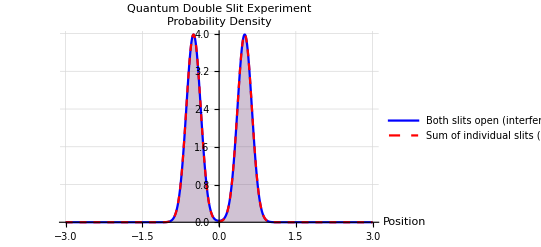

-Graphics-

-Graphics3D-

ListPlot::lpn: generateParticlePositions[100.,4.,4.] is not a list of numbers or pairs of numbers.

```mathematica
(* 1. Plot the probability distributions for various scenarios *)
probabilityPlot = Plot[{
    probabilityBothSlits[x, propagationTime, sigma],
    probabilitySumSeparate[x, propagationTime, sigma]
    }, {x, -3, 3},
    PlotRange -> All,
    PlotStyle -> {{Blue, Thick}, {Red, Dashed}},
    PlotLegends -> {
      "Both slits open (interference)", 
      "Sum of individual slits (no interference)"
    },
    PlotLabel -> "Quantum Double Slit Experiment",
    AxesLabel -> {"Position", "Probability Density"},
    GridLines -> Automatic,
    Filling -> {1 -> Axis, 2 -> Axis}
];

(* 2. Time evolution animation of the wavefunction *)
timeEvolutionAnimation = Animate[
  Plot[{
    probabilityBothSlits[x, t, sigma],
    probabilitySumSeparate[x, t, sigma]
    }, {x, -3, 3},
    PlotRange -> {0, 3},
    PlotStyle -> {{Blue, Thick}, {Red, Dashed}},
    PlotLegends -> {
      "Both slits open (interference)", 
      "Sum of individual slits (no interference)"
    },
    PlotLabel -> "Time Evolution of Quantum Double Slit: t = " <> ToString[t],
    AxesLabel -> {"Position", "Probability Density"},
    Filling -> {1 -> Axis, 2 -> Axis}
  ],
  {t, 0.01, 2, 0.1}
];

(* 3. Visualize the 2D interference pattern *)
(* Function to calculate intensity at a point on the detection screen *)
intensity2D[x_, y_, L_] := Module[{d = slitDistance, a = slitWidth, λ = wavelength},
  (* d is slit separation, a is slit width, λ is wavelength, L is screen distance *)
  (Sinc[Pi*a*Sqrt[x^2 + y^2]/(λ*L)]^2) * (Cos[Pi*d*x/(λ*L)]^2)
];

(* Generate the 2D interference pattern *)
screenDistance = 10;
interference2DPattern = DensityPlot[
  intensity2D[x, y, screenDistance], {x, -2, 2}, {y, -2, 2},
  PlotPoints -> 100,
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  PlotLabel -> "2D Double-Slit Interference Pattern",
  FrameLabel -> {{"y position", None}, {"x position", None}}
];

(* 4. 3D visualization of the 2D interference pattern *)
interference3DPattern = Plot3D[
  intensity2D[x, y, screenDistance], {x, -2, 2}, {y, -2, 2},
  PlotPoints -> 70,
  ColorFunction -> "TemperatureMap",
  PlotLabel -> "3D View of Double-Slit Interference",
  AxesLabel -> {"x position", "y position", "intensity"}
];

(* 5. Simulation of the buildup of an interference pattern one particle at a time *)
(* Define a function that simulates where a single particle might land *)
particleLanding[screenWidth_, screenHeight_] := Module[
  {x, y, prob, rnd},
  (* Choose a random position *)
  x = RandomReal[{-screenWidth/2, screenWidth/2}];
  y = RandomReal[{-screenHeight/2, screenHeight/2}];
  
  (* Calculate probability at this point *)
  prob = intensity2D[x, y, screenDistance];
  
  (* Use rejection sampling *)
  rnd = RandomReal[{0, 1}];
  If[rnd < prob, {x, y}, particleLanding[screenWidth, screenHeight]]
];

(* Generate positions for multiple particles *)
generateParticlePositions[n_, screenWidth_, screenHeight_] :=
  Table[particleLanding[screenWidth, screenHeight], {i, 1, n}]

(* Simulate the pattern buildup *)
particleBuildup = Manipulate[
  ListPlot[
    generateParticlePositions[n, 4, 4],
    PlotStyle -> {PointSize[0.005], Blue},
    PlotRange -> {{-2, 2}, {-2, 2}},
    AspectRatio -> 1,
    PlotLabel -> "Quantum Double-Slit: Buildup with " <> ToString[n] <> " Particles",
    AxesLabel -> {"x position", "y position"},
    Frame -> True
  ],
  {{n, 100, "Number of Particles"}, 10, 5000, 10, Appearance -> "Labeled"}
];

(* 6. Visualize wave function collapse *)
(* When we "measure" which slit the particle goes through *)
collapseAnimation = Manipulate[
  Plot[
    (1-measurement)*probabilityBothSlits[x, propagationTime, sigma] + 
    measurement*probabilitySumSeparate[x, propagationTime, sigma],
    {x, -3, 3},
    PlotRange -> {0, 3},
    PlotStyle -> {Blend[{Blue, Red}, measurement], Thick},
    PlotLabel -> "Effect of Measurement: " <> ToString[Round[100*measurement]] <> "% Collapse",
    AxesLabel -> {"Position", "Probability Density"},
    Filling -> Axis
  ],
  {{measurement, 0, "Measurement Strength"}, 0, 1, 0.01, Appearance -> "Labeled"}
];

(* Display the visualizations *)
probabilityPlot
interference2DPattern
interference3DPattern
particleBuildup
```

### The Measurement Paradox

The most astonishing aspect of the double - slit experiment emerges when we attempt to determine which path each particle takes . Let' s use Mathematica to illustrate what happens when we place detectors at the slits :

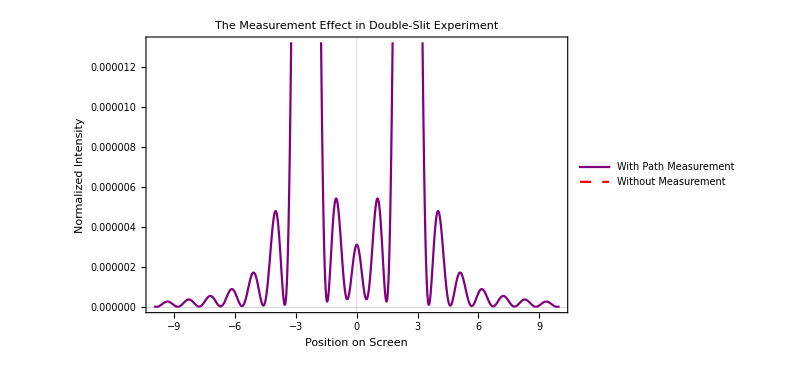

```mathematica
(* Function for single-slit pattern *)
singleSlitPattern[x_, slitPosition_] := 
Sinc[3 (x - slitPosition)]^2/10000;

(* Plot showing the effect of measurement *)
measuredPlot = Plot[
  {singleSlitPattern[x, -slitSeparation/2] + singleSlitPattern[x, slitSeparation/2], 
   probability[x]/Max[Table[probability[y], {y, -screenWidth/2, screenWidth/2, 0.1}]]},
  {x, -screenWidth/2, screenWidth/2},
  PlotStyle -> {{Thick, Purple}, {Thick, Red, Dashed}},
  PlotLegends -> {"With Path Measurement", "Without Measurement"},
  AxesLabel -> {"Position on Screen", "Normalized Intensity"},
  PlotLabel -> "The Measurement Effect in Double-Slit Experiment",
  PlotTheme -> "Scientific",
  ImageSize -> 600]
```

When we observe which slit each particle passes through, the interference pattern disappears, and we instead see the classical sum of two single - slit patterns . This demonstrates a fundamental principle of quantum mechanics : the act of measurement affects the system being measured .

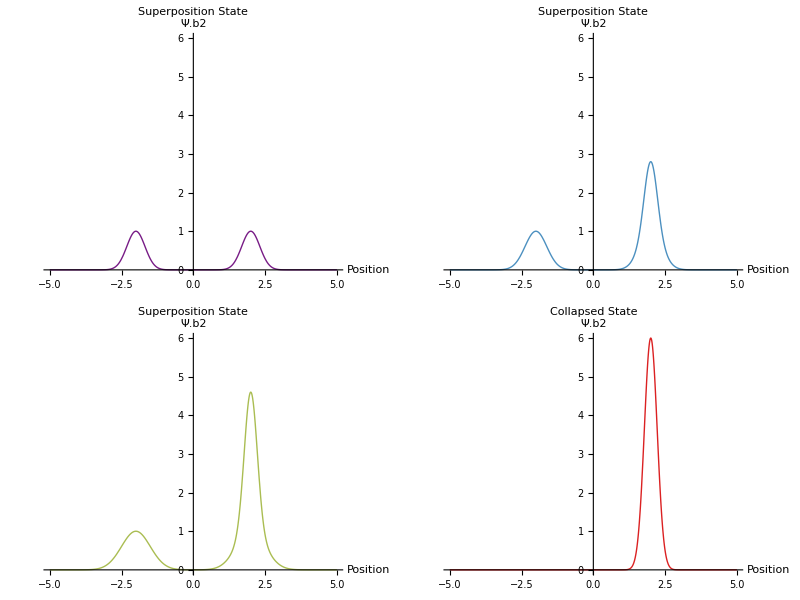

```mathematica
(* Visual representation of wavefunction collapse *)
animateCollapse = Manipulate[
  Plot[
    Exp[-5 (1 - t) (x - 2)^2] + Exp[-5 (1 - t) (x + 2)^2] + t*6*Exp[-10 (x - 2)^2] + If[t<1,0,-2],
    {x, -5, 5}, 
    PlotRange -> {0, 6},
    PlotLabel -> If[t < 1, "Superposition State", "Collapsed State"],
    AxesLabel -> {"Position", "Ψ.b2"},
    PlotStyle -> Directive[Thick, ColorData["Rainbow"][t]],
    ImageSize -> 500
  ],
  {t, 0, 1, 0.05}
]

frames = Table[
  Plot[
    Exp[-5 (1 - t) (x - 2)^2] + Exp[-5 (1 - t) (x + 2)^2] + t*6*Exp[-10 (x - 2)^2]+ If[t<1,0,-2],
    {x, -5, 5}, 
    PlotRange -> {0, 6},
    PlotLabel -> If[t < 1, "Superposition State", "Collapsed State"],
    AxesLabel -> {"Position", "Ψ.b2"},
    PlotStyle -> Directive[Thick, ColorData["Rainbow"][t]],
    ImageSize -> 350
  ],
  {t, {0, 0.3, 0.6, 1}}
];

Grid[{{frames[[1]], frames[[2]]}, {frames[[3]], frames[[4]]}}]
```

The double - slit experiment stands as one of the most elegant demonstrations that quantum mechanics represents a fundamental departure from classical physics . It forces us to reconsider our intuitive notions of reality and points to a quantum world that defies classical description.

## Heisenberg’s Uncertainty Principle

Werner Heisenberg formulated his famous uncertainty principle in 1927, establishing one of the fundamental limitations inherent in quantum mechanics . Unlike classical physics, where all properties of a system can in principle be measured with arbitrary precision, quantum mechanics reveals intrinsic limits to what can be simultaneously known about complementary variables. The uncertainty principle is most commonly expressed as a relationship between position (x) and momentum (p):

```mathematica
uncertaintyRelation = 
  HoldForm[Δx*Δp >= ℏ/2];

TraditionalForm[uncertaintyRelation]
```

Δx Δp≥ℏ/2

- Δx represents the standard deviation in position measurements
- Δp represents the standard deviation in momentum measurements
- ℏ is the reduced Planck constant (h/2π)
This inequality means that the more precisely we know a particle’s position, the less precisely we can know its momentum, and vice versa.
The principle applies to other complementary pairs of observables as well. For energy and time:

```mathematica
energyTimeUncertainty = 
  HoldForm[ΔE*Δt >= ℏ/2];

TraditionalForm[energyTimeUncertainty]
```

ΔE Δt≥ℏ/2

### Quantum Mechanical Basis

The uncertainty principle arises naturally from the wave nature of quantum entities. Let’s use Mathematica to visualize this concept through wavefunctions:

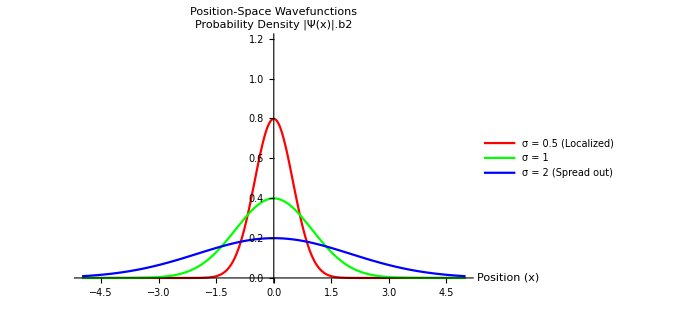

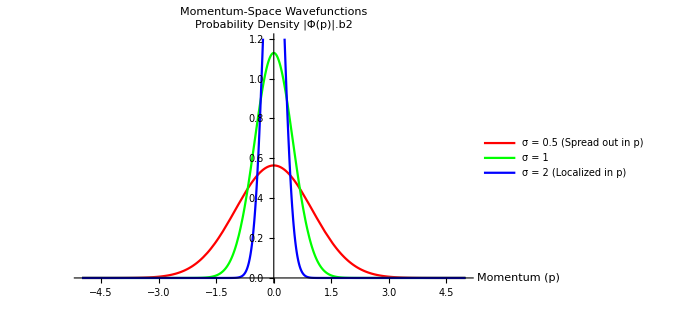

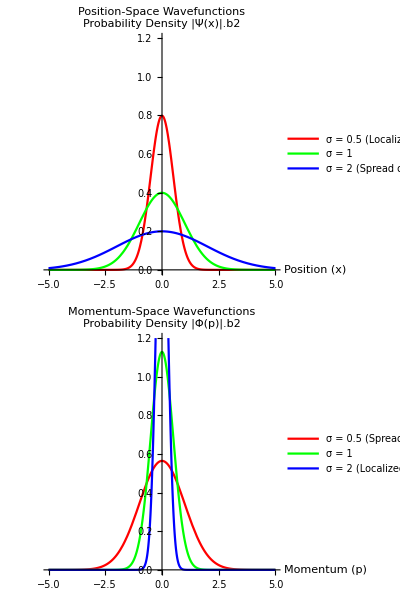

```mathematica
(* Define a Gaussian wavepacket *)
gaussianWavepacket[x_, σ_] := (2*Pi*σ^2)^(-1/4)*Exp[-x^2/(4*σ^2)];

(* Calculate momentum-space wavefunction (Fourier transform) *)
momentumWavefunction[p_, σ_] := (2*σ/Sqrt[Pi])^(1/2)*Exp[-p^2*σ^2];

(* Plot position-space wavefunctions with different widths *)
positionPlot = Plot[
  Evaluate[Table[
    Abs[gaussianWavepacket[x, σ]]^2, 
    {σ, {0.5, 1, 2}}
  ]],
  {x, -5, 5},
  PlotRange -> {0, 1.2},
  PlotStyle -> {Red, Green, Blue},
  PlotLegends -> 
    Placed[LineLegend[{Red, Green, Blue}, 
      {"σ = 0.5 (Localized)", "σ = 1", "σ = 2 (Spread out)"}], {0.5, 0.8}],
  AxesLabel -> {"Position (x)", "Probability Density |Ψ(x)|.b2"},
  PlotLabel -> "Position-Space Wavefunctions",
  ImageSize -> 500
]

(* Plot corresponding momentum-space wavefunctions *)
momentumPlot = Plot[
  Evaluate[Table[
    Abs[momentumWavefunction[p, σ]]^2, 
    {σ, {0.5, 1, 2}}
  ]],
  {p, -5, 5},
  PlotRange -> {0, 1.2},
  PlotStyle -> {Red, Green, Blue},
  PlotLegends -> 
    Placed[LineLegend[{Red, Green, Blue}, 
      {"σ = 0.5 (Spread out in p)", "σ = 1", "σ = 2 (Localized in p)"}], {0.5, 0.8}],
  AxesLabel -> {"Momentum (p)", "Probability Density |Φ(p)|.b2"},
  PlotLabel -> "Momentum-Space Wavefunctions",
  ImageSize -> 500
]

Grid[{{positionPlot}, {momentumPlot}}]
```

These plots illustrate that:
1. A wavefunction that is tightly localized in position-space (small σ, red curve in top plot) must be widely spread in momentum-space (red curve in bottom plot)
2. Conversely, a wavefunction widely spread in position-space (large σ, blue curve in top plot) can be more localized in momentum-space (blue curve in bottom plot)
This trade-off is a direct visual demonstration of the uncertainty principle.

## Core Principles of Quantum Mechanics

## Superposition Principle

The Superposition Principle states that any quantum system can exist in multiple states simultaneously until measured. Mathematically, if |ψ₁⟩ and |ψ₂⟩ are valid quantum states, then any linear combination a|ψ₁⟩ + b|ψ₂⟩ (where a and b are complex numbers satisfying |a|.b2 + |b|.b2 = 1) is also a valid quantum state.

This principle leads to:
1. Wave-like behavior of particles
2. Quantum interference effects
3. Multiple simultaneous outcomes for quantum systems
4. The need for probability amplitudes rather than classical probabilities

Superposition underlies many quantum phenomena, including tunneling, entanglement, and quantum computing.

```mathematica
(* Define a two-state quantum system *)
(* Basis states for a qubit (quantum bit) *)
Clear[ket0, ket1];
ket0 = {1, 0};  (* |0⟩ state *)
ket1 = {0, 1};  (* |1⟩ state *)

(* Create a superposition state with given probability amplitudes *)
superpositionState[alpha_, beta_] := Module[{normalization},
  (* Ensure normalization *)
  normalization = Sqrt[Abs[alpha]^2 + Abs[beta]^2];
  {alpha/normalization, beta/normalization}
]

(* Calculate probability of measuring each basis state *)
probability0[state_] := Abs[state[[1]]]^2
probability1[state_] := Abs[state[[2]]]^2

(* Example superposition states *)
equalSuperposition = superpositionState[1, 1]
skewedSuperposition = superpositionState[2, 1]
complexSuperposition = superpositionState[1, I]
```

{1/(√2),1/(√2)}

{2/(√5),1/(√5)}

{1/(√2),ⅈ/(√2)}

### Visualization

```mathematica
(* Convert state vector to Bloch sphere coordinates *)
stateToBlochCoordinates[state_] := Module[{theta, phi, r, i},
  (* Extract real and imaginary parts of the coefficients *)
  r = Re[state[[2]]/state[[1]]];
  i = Im[state[[2]]/state[[1]]];
  
  (* Convert to spherical coordinates *)
  theta = 2 * ArcTan[Sqrt[r^2 + i^2]];
  phi = ArcTan[i, r];
  
  {Sin[theta]*Cos[phi], Sin[theta]*Sin[phi], Cos[theta]}
]

(* Function to create a Bloch sphere with a state vector *)
createBlochSphere[state_] := Module[{coords, arrows, sphere, axes},
  coords = stateToBlochCoordinates[state];
  
  (* Create the Bloch sphere *)
  sphere = Graphics3D[{Opacity[0.3], Sphere[{0, 0, 0}, 1]}];
  
  (* Create coordinate axes *)
  axes = Graphics3D[{
    {Thick, Arrow[{{0, 0, 0}, {1.5, 0, 0}}]},
    {Thick, Arrow[{{0, 0, 0}, {0, 1.5, 0}}]},
    {Thick, Arrow[{{0, 0, 0}, {0, 0, 1.5}}]},
    Text["x", {1.6, 0, 0}],
    Text["y", {0, 1.6, 0}],
    Text["z", {0, 0, 1.6}]
  }];
  
  (* Create the state vector arrow *)
  arrows = Graphics3D[{
    {Red, Thick, Arrow[{{0, 0, 0}, coords}]},
    {Red, PointSize[0.02], Point[coords]}
  }];
  
  (* Combine all elements *)
  Show[sphere, axes, arrows,
    PlotRange -> {{-1.5, 1.5}, {-1.5, 1.5}, {-1.5, 1.5}},
    Axes -> False,
    BoxRatios -> {1, 1, 1},
    PlotLabel -> "Bloch Sphere Representation"
  ]
]
```

```mathematica
superpositionVisualizer = Manipulate[
  Module[{state, probabilities, blochSphere, barChart},
    state = superpositionState[a + I*b, c + I*d];
    probabilities = {probability0[state], probability1[state]};
    
    blochSphere = createBlochSphere[state];
    
    barChart = BarChart[probabilities,
      PlotLabel -> "Measurement Probabilities",
      ChartLabels -> {"State |0⟩", "State |1⟩"},
      PlotRange -> {0, 1},
      BarOrigin -> Bottom,
      ChartStyle -> "Pastel"
    ];
    
    Grid[{
      {blochSphere, barChart},
      {Text["State Vector: " <> ToString[state, InputForm]], SpanFromLeft}
    }]
  ],
  {{a, 1, "Re(α)"}, -2, 2, 0.1},
  {{b, 0, "Im(α)"}, -2, 2, 0.1},
  {{c, 1, "Re(β)"}, -2, 2, 0.1},
  {{d, 0, "Im(β)"}, -2, 2, 0.1}
]
```

#### Visualization of Quantum superposition in a Double-Well Potential

```mathematica
(* Wavefunctions for the first two energy eigenstates *)
psi0[x_] := (1/Sqrt[Pi])^(1/4) * Exp[-x^2/2]  (* Ground state *)
psi1[x_] := (1/Sqrt[Pi])^(1/4) * Sqrt[2] * x * Exp[-x^2/2]  (* First excited state *)

(* Potential well *)
doubleWell[x_] := (x^2 - 2)^2

(* Superposition of states *)
superpositionWavefunction[x_, a_, b_, phase_] := 
  a * psi0[x] + b * Exp[I * phase] * psi1[x]

(* Probability density *)
probDensity[x_, a_, b_, phase_] := 
  Abs[superpositionWavefunction[x, a, b, phase]]^2

(* Visualization of superposition in a double well *)
doubleWellVisualization = Manipulate[
  Plot[{
    5 * probDensity[x, alpha, beta, phase] - 8,  (* Scaled probability density *)
    doubleWell[x]  (* Potential well *)
    }, 
    {x, -3, 3},
    PlotRange -> {{-3, 3}, {-10, 10}},
    PlotStyle -> {{Red, Thick}, {Blue, Thick}},
    Filling -> {1 -> -8},
    FillingStyle -> Opacity[0.3, Red],
    PlotLegends -> {"Probability Density", "Double Well Potential"},
    PlotLabel -> "Quantum Superposition in Double Well",
    AxesLabel -> {"Position", "Energy/Probability"}
  ],
  {{alpha, 1/Sqrt[2], "ψ₀ coefficient"}, 0, 1, 0.01},
  {{beta, 1/Sqrt[2], "ψ₁ coefficient"}, 0, 1, 0.01},
  {{phase, 0, "Relative Phase"}, 0, 2Pi, 0.1},
  Initialization :> (
    (* Ensure normalization *)
    Dynamic[
      norm = Sqrt[alpha^2 + beta^2];
      alpha = alpha/norm;
      beta = beta/norm;
    ]
  )
]
```

## Quantum Measurement and Collapse

Quantum Measurement is a process that fundamentally differs from classical observation:

1. Prior to measurement, quantum systems exist in superpositions of multiple states
2. Upon measurement, the wavefunction “collapses” to one of the eigenstates of the measured observable
3. The probability of collapsing to a particular eigenstate is |⟨ψ|ϕ⟩|.b2, where |ψ⟩ is the system state and |ϕ⟩ is the eigenstate
4. After measurement, the system remains in the collapsed state for subsequent measurements of the same observable

This measurement process:
- Is inherently probabilistic (non-deterministic)
- Is irreversible
- Introduces the observer or measurement apparatus into the physical description
- Relates to the broader “measurement problem” in quantum interpretation

```mathematica
(* Simulate quantum measurement of a qubit *)
measureQubit[state_] := Module[{p0, randomNum},
  p0 = probability0[state];
  randomNum = RandomReal[];
  
  (* Return the post-measurement state *)
  If[randomNum < p0,
    {1, 0},  (* Collapsed to |0⟩ *)
    {0, 1}   (* Collapsed to |1⟩ *)
  ]
]

(* Function to simulate multiple measurements of identically prepared qubits *)
multipleQubitMeasurements[state_, numMeasurements_] := 
  Table[measureQubit[state], {i, 1, numMeasurements}]

(* Calculate measurement statistics *)
measurementStatistics[measurements_] := Module[{zeros, ones},
  zeros = Count[measurements, {1, 0}];
  ones = Count[measurements, {0, 1}];
  {zeros/Length[measurements], ones/Length[measurements]}
]
```

### Prepare a State and Perform Measurements

```mathematica
exampleState = superpositionState[Sqrt[3], 1];
exampleMeasurements = multipleQubitMeasurements[exampleState, 1000];
exampleStats = measurementStatistics[exampleMeasurements];
```

### Visualization

#### Visualization of the Measurement Process

```mathematica
measurementProcess = Manipulate[
  Module[{initialState, p0, p1, measurementResult, finalState, 
    initialBloch, finalBloch, probChart, resultText},
    
    initialState = superpositionState[a + I*b, c + I*d];
    {p0, p1} = {probability0[initialState], probability1[initialState]};
    
    (* Determine measurement outcome based on slider *)
    measurementResult = 
      If[measureStrength < p0, {1, 0}, {0, 1}];
    
    (* Interpolate between initial and final states *)
    finalState = measurementResult;
    
    (* The "collapse" progress from initial to final state *)
    collapsingState = 
      (1 - collapseProgress) * initialState + 
      collapseProgress * finalState;
    
    (* Create visualizations *)
    initialBloch = createBlochSphere[initialState];
    collapsingBloch = createBlochSphere[collapsingState/Norm[collapsingState]];
    
    probChart = BarChart[{p0, p1},
      PlotLabel -> "Measurement Probabilities",
      ChartLabels -> {"State |0⟩", "State |1⟩"},
      PlotRange -> {0, 1},
      ChartStyle -> "Pastel"
    ];
    
    resultText = If[measureStrength < p0,
      Style["Measurement Result: State |0⟩", Bold, Blue],
      Style["Measurement Result: State |1⟩", Bold, Red]
    ];
    
    Grid[{
      {collapsingBloch, probChart},
      {resultText, SpanFromLeft},
      {Text["Collapse Progress: " <> ToString[collapseProgress]], SpanFromLeft}
    }]
  ],
  {{a, 1, "Re(α)"}, -2, 2, 0.1, Enabled -> True},
  {{b, 0, "Im(α)"}, -2, 2, 0.1, Enabled -> True},
  {{c, 1, "Re(β)"}, -2, 2, 0.1, Enabled -> True},
  {{d, 0, "Im(β)"}, -2, 2, 0.1, Enabled -> True},
  {{measureStrength, 0.5, "Random Number for Measurement"}, 0, 1, 0.01, Enabled -> True},
  {{collapseProgress, 0, "Collapse Progress"}, 0, 1, 0.01, Enabled -> True}
]
```

#### Visualization of Multiple Measurements

```mathematica
simulationResults = Manipulate[
  Module[{state, measurements, stats, theoreticalProb, comparisonChart},
    state = superpositionState[Cos[theta], Sin[theta]*Exp[I*phi]];
    measurements = multipleQubitMeasurements[state, numMeasurements];
    stats = measurementStatistics[measurements];
    theoreticalProb = {probability0[state], probability1[state]};
    
    comparisonChart = BarChart[{
      {theoreticalProb[[1]], stats[[1]]},
      {theoreticalProb[[2]], stats[[2]]}
      },
      ChartLayout -> "Grouped",
      ChartLabels -> {{"State |0⟩", "State |1⟩"}, {"Theoretical", "Observed"}},
      PlotLabel -> "Quantum Measurement Statistics\n" <> 
                  ToString[numMeasurements] <> " Measurements",
      PlotRange -> {0, 1},
      ChartStyle -> {Blue, Red}
    ];
    
    Grid[{
      {createBlochSphere[state], comparisonChart},
      {
       Text["Theoretical Probabilities: " <> ToString[theoreticalProb]]}
    }]
  ],
  {{theta, Pi/4, "θ (state angle)"}, 0, Pi, 0.01},
  {{phi, 0, "φ (phase angle)"}, 0, 2Pi, 0.01},
  {{numMeasurements, 100, "Number of Measurements"}, {10, 100, 1000, 10000}}
]
```

#### Visualization of Wavefunction Collapse for a Particle in a Box

```mathematica
(* Wavefunctions for a particle in a box *)
particleInBoxWavefunction[n_, x_] := 
  Sqrt[2] * Sin[n * Pi * x]

(* Superposition of eigenstates *)
boxSuperposition[x_, coefficients_] := 
  Sum[coefficients[[n]] * particleInBoxWavefunction[n, x], {n, 1, Length[coefficients]}]

(* Probability density *)
boxProbabilityDensity[x_, coefficients_] := 
  Abs[boxSuperposition[x, coefficients]]^2

(* Visualization of wavefunction collapse *)
wavefunctionCollapseVisualization = Manipulate[
  Module[{initialCoeffs, measuredState, initialWF, measuredWF, initialProb, measuredProb},
    initialCoeffs = {c1, c2, c3, c4, c5}/Sqrt[c1^2 + c2^2 + c3^2 + c4^2 + c5^2];
    
    (* Calculate probability of each eigenstate *)
    probabilities = initialCoeffs^2;
    
    (* For "measured" state, only one eigenstate remains *)
    measuredState = Table[If[i == measuredEigenstate, 1, 0], {i, 1, 5}];
    
    (* Calculate wavefunctions and probabilities *)
    initialWF[x_] := boxSuperposition[x, initialCoeffs];
    measuredWF[x_] := boxSuperposition[x, measuredState];
    
    initialProb[x_] := boxProbabilityDensity[x, initialCoeffs];
    measuredProb[x_] := boxProbabilityDensity[x, measuredState];
    
    (* Interpolate between initial and measured states based on collapse progress *)
    interpolatedWF[x_] := 
      (1 - collapseProgress) * initialWF[x] + collapseProgress * measuredWF[x];
    
    interpolatedProb[x_] := Abs[interpolatedWF[x]]^2;
    
    (* Create plots *)
    Grid[{
      {
        Plot[initialProb[x], {x, 0, 1},
          PlotRange -> {{0, 1}, {0, 3}},
          PlotLabel -> "Initial Probability Density",
          AxesLabel -> {"Position", "Probability Density"},
          PlotStyle -> Blue,
          Filling -> Axis,
          FillingStyle -> Opacity[0.3, Blue]
        ],
        Plot[measuredProb[x], {x, 0, 1},
          PlotRange -> {{0, 1}, {0, 3}},
          PlotLabel -> "Collapsed to Eigenstate " <> ToString[measuredEigenstate],
          AxesLabel -> {"Position", "Probability Density"},
          PlotStyle -> Red,
          Filling -> Axis,
          FillingStyle -> Opacity[0.3, Red]
        ]
      },
      {
        Plot[interpolatedProb[x], {x, 0, 1},
          PlotRange -> {{0, 1}, {0, 3}},
          PlotLabel -> "Wavefunction During Collapse (Progress: " <> 
                     ToString[Round[collapseProgress, 0.01]] <> ")",
          AxesLabel -> {"Position", "Probability Density"},
          PlotStyle -> Purple,
          Filling -> Axis,
          FillingStyle -> Opacity[0.3, Purple]
        ],
        BarChart[probabilities,
          PlotLabel -> "Initial Probabilities for Each Eigenstate",
          ChartLabels -> Table["n=" <> ToString[i], {i, 1, Length[probabilities]}],
          PlotRange -> {0, 1},
          ChartStyle -> ColorData[112]
        ]
      }
    }]
  ],
  {{c1, 1, "Coefficient 1"}, 0, 1, 0.01},
  {{c2, 0.7, "Coefficient 2"}, 0, 1, 0.01},
  {{c3, 0.5, "Coefficient 3"}, 0, 1, 0.01},
  {{c4, 0.3, "Coefficient 4"}, 0, 1, 0.01},
  {{c5, 0.1, "Coefficient 5"}, 0, 1, 0.01},
  {{measuredEigenstate, 1, "Measured Eigenstate"}, {1, 2, 3, 4, 5}},
  {{collapseProgress, 0, "Collapse Progress"}, 0, 1, 0.01}
]
```

## Quantum Entanglement

Quantum Entanglement occurs when two or more quantum systems become correlated in such a way that the quantum state of each particle cannot be described independently of the others, regardless of the distance separating them .
  
  Key aspects :
  1. A measurement on one entangled particle instantaneously affects its entangled partners
2. Einstein called this "spooky action at a distance" - suggesting quantum mechanics was incomplete
3. Bell' s Theorem and subsequent experiments proved that entanglement cannot be explained by local hidden variables
4. Entanglement enables quantum technologies like quantum teleportation and super - dense coding

The archetypal entangled state is the Bell state :
   | Φ⁺⟩ = (| 00 ⟩ + | 11 ⟩)/√2

When measured in the same basis, entangled particles always show correlated results, even when separated by arbitrarily large distances .

```mathematica
(* Define common two-qubit Bell states *)
bellStatePhi1 = 1/Sqrt[2] * {1, 0, 0, 1};  (* |Φ⁺⟩ = (|00⟩ + |11⟩)/√2 *)
bellStatePhi2 = 1/Sqrt[2] * {1, 0, 0, -1}; (* |Φ⁻⟩ = (|00⟩ - |11⟩)/√2 *)
bellStatePsi1 = 1/Sqrt[2] * {0, 1, 1, 0};  (* |Ψ⁺⟩ = (|01⟩ + |10⟩)/√2 *)
bellStatePsi2 = 1/Sqrt[2] * {0, 1, -1, 0}; (* |Ψ⁻⟩ = (|01⟩ - |10⟩)/√2 *)

(* Function to measure a Bell state - returns the measurement outcomes for both qubits *)
measureBellState[bellState_] := Module[{prob00, prob01, prob10, prob11, randomNum},
  (* Calculate probabilities of each outcome *)
  prob00 = Abs[bellState[[1]]]^2;
  prob01 = Abs[bellState[[2]]]^2;
  prob10 = Abs[bellState[[3]]]^2;
  prob11 = Abs[bellState[[4]]]^2;
  
  (* Generate a random measurement outcome *)
  randomNum = RandomReal[];
  
  (* Return measurement results for both qubits *)
  Which[
    randomNum < prob00, {{1, 0}, {1, 0}},  (* Both qubits measured as |0⟩ *)
    randomNum < prob00 + prob01, {{1, 0}, {0, 1}},  (* First |0⟩, second |1⟩ *)
    randomNum < prob00 + prob01 + prob10, {{0, 1}, {1, 0}},  (* First |1⟩, second |0⟩ *)
    True, {{0, 1}, {0, 1}}  (* Both qubits measured as |1⟩ *)
  ]
]

(* Simulate multiple measurements of a Bell state *)
multipleBellMeasurements[bellState_, numMeasurements_] := 
  Table[measureBellState[bellState], {i, 1, numMeasurements}]

(* Function to analyze correlations in Bell state measurements *)
analyzeCorrelations[measurements_] := Module[{sameResults, diffResults},
  sameResults = Count[measurements, {{1, 0}, {1, 0}} | {{0, 1}, {0, 1}}];
  diffResults = Count[measurements, {{1, 0}, {0, 1}} | {{0, 1}, {1, 0}}];
  {sameResults/Length[measurements], diffResults/Length[measurements]}
]
```

### Visualization

#### Visualization of Bell State Measurement Correlation

```mathematica
bellStateVisualizer = Manipulate[
  Module[{state, measurements, correlations, correlationPlot, densityMatrix, densityPlot},
    (* Create a custom Bell state *)
    state = Normalize[{a, b, c, d}];
    
    (* Perform measurements *)
    measurements = multipleBellMeasurements[state, numMeasurements];
    correlations = analyzeCorrelations[measurements];
    
    (* Create visualization of correlations *)
    correlationPlot = BarChart[correlations,
      PlotLabel -> "Measurement Correlations",
      ChartLabels -> {"Same Result", "Different Result"},
      AxesLabel -> {"", "Probability"},
      PlotRange -> {0, 1},
      ChartStyle -> {Blue, Red}
    ];
    
    (* Compute and visualize the density matrix *)
    densityMatrix = KroneckerProduct[state, ConjugateTranspose[state]];
    densityPlot = MatrixPlot[Abs[densityMatrix],
      PlotLabel -> "Density Matrix (Absolute Values)",
      ColorFunction -> "Temperature"
    ];
    
    Grid[{
      {densityPlot, correlationPlot},
      {Text["State: " <> ToString[state, InputForm]]},{
       Text["Number of Measurements: " <> ToString[numMeasurements]]}
    }]
  ],
  {{a, 1/Sqrt[2], "Coefficient |00⟩"}, -1, 1, 0.1},
  {{b, 0, "Coefficient |01⟩"}, -1, 1, 0.1},
  {{c, 0, "Coefficient |10⟩"}, -1, 1, 0.1},
  {{d, 1/Sqrt[2], "Coefficient |11⟩"}, -1, 1, 0.1},
  {{numMeasurements, 1000, "Number of Measurements"}, {100, 1000, 10000}}
]
```

#### Quantum Teleportation Visualization

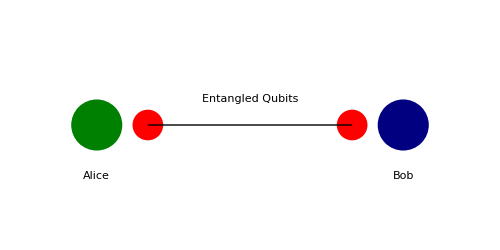
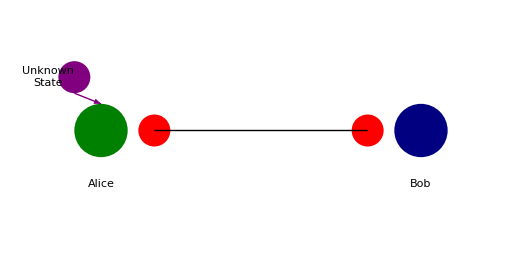
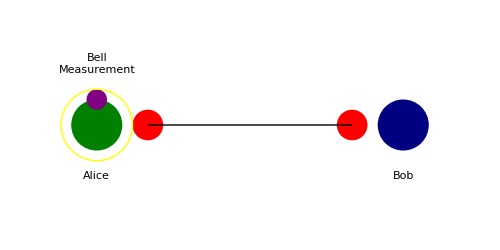
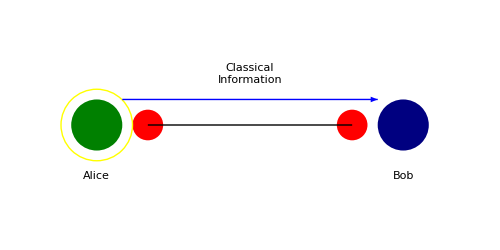
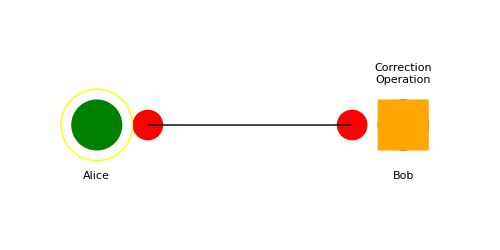
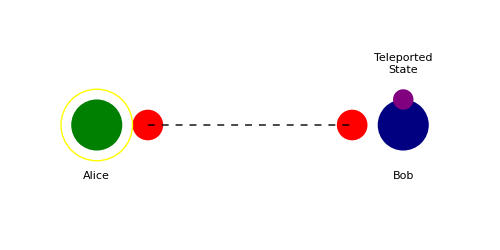
Quantum Teleportation Process
Created by: thisismeamir
Date: 2025-05-05 07:13:15 UTC

-Graphics- | Step 1: Alice and Bob share an entangled pair of qubits.
-Graphics- | Step 2: Alice receives an unknown quantum state to teleport.
-Graphics- | Step 3: Alice performs a Bell measurement on her qubit and the unknown state.
-Graphics- | Step 4: Alice sends classical measurement results to Bob.
-Graphics- | Step 5: Bob applies a correction operation based on the classical information.
-Graphics- | Step 6: Bob's qubit is now in the unknown quantum state. Teleportation is complete!

```mathematica
(*Create a list of frames for quantum teleportation*)Module[{frames,captions},frames={(*Step 1*)Graphics[{(*Alice,Bob and their entangled qubits*){RGBColor[0,0.5,0],Disk[{-3,0},0.5]},(*Dark Green*){RGBColor[0,0,0.5],Disk[{3,0},0.5]},(*Dark Blue*)Text["Alice",{-3,-1}],Text["Bob",{3,-1}],{RGBColor[1,0,0],Disk[{-2,0},0.3]},(*Red*){RGBColor[1,0,0],Disk[{2,0},0.3]},(*Red*){GrayLevel[0],Line[{{-2,0},{2,0}}]},(*Black*)Text["Entangled Qubits",{0,0.5}]},PlotRange->{{-4,4},{-2,2}},ImageSize->500],(*Step 2*)Graphics[{(*Alice receives an unknown state*){RGBColor[0,0.5,0],Disk[{-3,0},0.5]},{RGBColor[0,0,0.5],Disk[{3,0},0.5]},Text["Alice",{-3,-1}],Text["Bob",{3,-1}],{RGBColor[1,0,0],Disk[{-2,0},0.3]},{RGBColor[1,0,0],Disk[{2,0},0.3]},{GrayLevel[0],Line[{{-2,0},{2,0}}]},{RGBColor[0.5,0,0.5],Disk[{-3.5,1},0.3]},(*Purple*){RGBColor[0.5,0,0.5],Arrow[{{-3.5,0.7},{-3,0.5}}]},Text["Unknown\nState",{-4,1}]},PlotRange->{{-4,4},{-2,2}},ImageSize->500],(*Step 3*)Graphics[{(*Alice performs Bell measurement*){RGBColor[0,0.5,0],Disk[{-3,0},0.5]},{RGBColor[0,0,0.5],Disk[{3,0},0.5]},Text["Alice",{-3,-1}],Text["Bob",{3,-1}],{RGBColor[1,0,0],Disk[{-2,0},0.3]},{RGBColor[1,0,0],Disk[{2,0},0.3]},{GrayLevel[0],Line[{{-2,0},{2,0}}]},{RGBColor[0.5,0,0.5],Disk[{-3,0.5},0.2]},{RGBColor[1,1,0],Circle[{-3,0},0.7]},(*Yellow*)Text["Bell\nMeasurement",{-3,1.2}]},PlotRange->{{-4,4},{-2,2}},ImageSize->500],(*Step 4*)Graphics[{(*Alice sends classical information to Bob*){RGBColor[0,0.5,0],Disk[{-3,0},0.5]},{RGBColor[0,0,0.5],Disk[{3,0},0.5]},Text["Alice",{-3,-1}],Text["Bob",{3,-1}],{RGBColor[1,0,0],Disk[{-2,0},0.3]},{RGBColor[1,0,0],Disk[{2,0},0.3]},{GrayLevel[0],Line[{{-2,0},{2,0}}]},{RGBColor[1,1,0],Circle[{-3,0},0.7]},{RGBColor[0,0,1],Arrow[{{-2.5,0.5},{2.5,0.5}}]},(*Blue*)Text["Classical\nInformation",{0,1}]},PlotRange->{{-4,4},{-2,2}},ImageSize->500],(*Step 5*)Graphics[{(*Bob applies correction based on classical information*){RGBColor[0,0.5,0],Disk[{-3,0},0.5]},{RGBColor[0,0,0.5],Disk[{3,0},0.5]},Text["Alice",{-3,-1}],Text["Bob",{3,-1}],{RGBColor[1,0,0],Disk[{-2,0},0.3]},{RGBColor[1,0,0],Disk[{2,0},0.3]},{GrayLevel[0],Line[{{-2,0},{2,0}}]},{RGBColor[1,1,0],Circle[{-3,0},0.7]},{RGBColor[1,0.65,0],Rectangle[{2.5,-0.5},{3.5,0.5}]},(*Orange*)Text["Correction\nOperation",{3,1}]},PlotRange->{{-4,4},{-2,2}},ImageSize->500],(*Step 6*)Graphics[{(*Final state:Unknown state teleported to Bob*){RGBColor[0,0.5,0],Disk[{-3,0},0.5]},{RGBColor[0,0,0.5],Disk[{3,0},0.5]},Text["Alice",{-3,-1}],Text["Bob",{3,-1}],{RGBColor[1,0,0],Disk[{-2,0},0.3]},{RGBColor[1,0,0],Disk[{2,0},0.3]},{GrayLevel[0],Dashed,Line[{{-2,0},{2,0}}]},{RGBColor[1,1,0],Circle[{-3,0},0.7]},{RGBColor[0.5,0,0.5],Disk[{3,0.5},0.2]},Text["Teleported\nState",{3,1.2}]},PlotRange->{{-4,4},{-2,2}},ImageSize->500]};
captions={"Step 1: Alice and Bob share an entangled pair of qubits.","Step 2: Alice receives an unknown quantum state to teleport.","Step 3: Alice performs a Bell measurement on her qubit and the unknown state.","Step 4: Alice sends classical measurement results to Bob.","Step 5: Bob applies a correction operation based on the classical information.","Step 6: Bob's qubit is now in the unknown quantum state. Teleportation is complete!"};
(*Create Column with Title*)Column[{Style["Quantum Teleportation Process",Bold,24],Style["Created by: thisismeamir",Italic,12],Style["Date: 2025-05-05 07:13:15 UTC",Italic,12],Spacer[20],Grid[Transpose[{frames,Style[#,Bold,14]&/@captions}],Spacings->{2,2},Alignment->{Center,Center}]},Alignment->Center,Spacings->2]]
```

## The Correspondence Principle

The Correspondence Principle, formulated by Niels Bohr, states that quantum mechanics must reduce to classical physics in the limit of large quantum numbers or macroscopic systems. This principle served as a guiding heuristic in the development of quantum theory.
Key aspects:
1. As quantum numbers become large, quantum predictions approach classical predictions
2. Quantum systems with high energy or large size behave increasingly classically
3. The principle helps bridge the conceptual gap between the quantum and classical domains
4. It explains why we don’t observe quantum effects in everyday (macroscopic) objects

Examples of the correspondence principle in action:
- Angular momentum quantization becomes negligible for large quantum numbers
- Quantum oscillator energy levels become effectively continuous at high energies
- Electron orbitals approach classical orbits for large principal quantum numbers
- Wave packets with large quantum numbers follow nearly classical trajectories

### Compare Quantum and Classical Probability Distributions

```mathematica
probabilityComparisonPlot = Manipulate[
  Module[{quantumProb, classicalProb, classicalA},
    (* Calculate equivalent classical amplitude for this quantum number *)
    classicalA = Sqrt[(2*n + 1) * hbar/(m*omega)];
    
    (* Plot quantum probability density *)
    quantumProb = Plot[quantumProbabilityDensity[n, x], {x, -4, 4},
      PlotStyle -> {Blue, Thick},
      PlotRange -> {{-4, 4}, {0, 1}},
      PlotLabel -> "n = " <> ToString[n] <> ": Quantum vs Classical Probability Density",
      AxesLabel -> {"Position", "Probability Density"},
      Filling -> Axis,
      FillingStyle -> Opacity[0.2, Blue]
    ];
    
    (* Plot classical probability density *)
    classicalProb = Plot[
      If[Abs[x] < classicalA, classicalPositionProbability[x, classicalA], 0], 
      {x, -4, 4},
      PlotStyle -> {Red, Thick},
      Filling -> Axis,
      FillingStyle -> Opacity[0.2, Red]
    ];
    
    (* Combine plots *)
    Show[quantumProb, classicalProb,
      PlotLegends -> {"Quantum Probability", "Classical Probability"},
      ImageSize -> 500
    ]
  ],
  {{n, 0, "Quantum Number n"}, 0, 30, 1}
]
```

### Visualize Wave Packets Approaching Classical Trajectories

```mathematica
(* Time-dependent wave packet for a free particle *)
gaussianWavePacket[x_, t_, x0_, k0_, sigma_] := 
  1/(Sqrt[sigma * Sqrt[Pi] * (1 + I*hbar*t/(m*sigma^2))]) * 
  Exp[-(x - x0 - hbar*k0*t/m)^2/(2*sigma^2*(1 + I*hbar*t/(m*sigma^2))) + I*k0*x - I*hbar*k0^2*t/(2*m)]

(* Probability density for the wave packet *)
wavePacketProbability[x_, t_, x0_, k0_, sigma_] := 
  Abs[gaussianWavePacket[x, t, x0, k0, sigma]]^2

(* Animate wave packet evolution *)
wavePacketAnimation = Manipulate[
  Module[{classicalPosition, quantumPlot, classicalPlot},
    (* Classical particle position at time t *)
    classicalPosition = x0 + velocity * t;
    
    (* Plot quantum wave packet *)
    quantumPlot = Plot[wavePacketProbability[x, t, x0, k0, sigma], {x, -10, 30},
      PlotStyle -> {Blue, Thick},
      PlotRange -> {{-10, 30}, {0, 0.5}},
      AxesLabel -> {"Position", "Probability Density"},
      PlotLabel -> "Correspondence Principle: Wave Packet Motion\nTime = " <> ToString[t],
      Filling -> Axis,
      FillingStyle -> Opacity[0.2, Blue]
    ];
    
    (* Show classical position *)
    classicalPlot = Graphics[{
      {Red, PointSize[0.02], Point[{classicalPosition, 0}]},
      {Red, Dashed, Line[{{classicalPosition, 0}, {classicalPosition, 0.5}}]},
      Text["Classical Position", {classicalPosition, 0.45}]
    }];
    
    (* Combine plots *)
    Show[quantumPlot, classicalPlot, ImageSize -> 500]
  ],
  {{t, 0, "Time"}, 0, 10, 0.1},
  {{sigma, 1, "Wave Packet Width"}, 0.1, 3, 0.1},
  {{x0, 0, "Initial Position"}, -5, 5, 1},
  {{k0, 2, "Initial Momentum"}, 0, 5, 0.5},
  Initialization :> (
    velocity = hbar * k0 / m  (* Calculate classical velocity *)
  )
]
```

## Mathematical Foundations of Quantum Mechanics

## Introduction to Hilbert Spaces

In quantum mechanics, physical states are represented as vectors in a complex vector space called a Hilbert space . A Hilbert space is a complete inner product space, which means :
  
  1. It is a vector space (elements can be added and multiplied by scalars)
2. It has an inner product that assigns a complex number to any pair of vectors
3. It is complete (all Cauchy sequences converge)

For finite - dimensional systems (like spin), the Hilbert space is simply ℂ^n . For continuous systems (like position), we work with infinite - dimensional spaces of square - integrable functions .
   
   The key feature of Hilbert spaces that makes them suitable for quantum mechanics is that they naturally incorporate the concept of probability amplitudes through their inner product structure. Let’s visualize a simple two-dimensional Hilbert space (representing a qubit)

```mathematica
(* Define the computational basis states *)
ket0 = {1, 0};
ket1 = {0, 1};

(* Define some quantum states *)
psi1 = 1/Sqrt[2] (ket0 + ket1); (* |+⟩ state *)
psi2 = 1/Sqrt[2] (ket0 - ket1); (* |-⟩ state *)
psi3 = 1/Sqrt[2] (ket0 + I*ket1); (* |+i⟩ state *)
psi4 = 1/Sqrt[2] (ket0 - I*ket1); (* |-i⟩ state *)

(* Inner product example *)
InnerProduct[v1_, v2_] := Conjugate[v1].v2
Print["Inner product ⟨+|+i⟩ = ", InnerProduct[psi1, psi3]]
Print["Probability amplitude = ", Abs[InnerProduct[psi1, psi3]]^2]

(* Represent the states on the Bloch sphere *)
BlochSphereRepresentation[{a_, b_}] := Module[
  {theta, phi},
  If[a == 0, {0, 0, 1},
   theta = 2*ArcCos[Abs[a]];
   phi = Arg[b/a];
   {Sin[theta]*Cos[phi], Sin[theta]*Sin[phi], Cos[theta]}
  ]
]

(* Convert our states to Bloch sphere coordinates *)
bloch1 = BlochSphereRepresentation[psi1];
bloch2 = BlochSphereRepresentation[psi2];
bloch3 = BlochSphereRepresentation[psi3];
bloch4 = BlochSphereRepresentation[psi4];

(* Create a visualization of the states on the Bloch sphere *)
blochSphere = Graphics3D[{
   {Opacity[0.3], Sphere[]},
   {Red, Arrowheads[0.05], Arrow[{{0, 0, 0}, bloch1}], Text["|+⟩", 1.1*bloch1]},
   {Blue, Arrowheads[0.05], Arrow[{{0, 0, 0}, bloch2}], Text["|-⟩", 1.1*bloch2]},
   {Green, Arrowheads[0.05], Arrow[{{0, 0, 0}, bloch3}], Text["|+i⟩", 1.1*bloch3]},
   {Orange, Arrowheads[0.05], Arrow[{{0, 0, 0}, bloch4}], Text["|-i⟩", 1.1*bloch4]},
   {Black, Arrowheads[0.05], Arrow[{{0, 0, 0}, {0, 0, 1}}], Text["|0⟩", {0, 0, 1.1}]},
   {Black, Arrowheads[0.05], Arrow[{{0, 0, 0}, {0, 0, -1}}], Text["|1⟩", {0, 0, -1.1}]}
   },
   PlotRange -> 1.2,
   Boxed -> False,
   Lighting -> "Neutral"
];

blochSphere
```

Inner product ⟨+|+i⟩ = 1/2+ⅈ/2

Probability amplitude = 1/2

-Graphics3D-

## State Vectors and Wave Functions

In quantum mechanics, a pure state is represented by a state vector |ψ⟩ in a Hilbert space (using Dirac’s bra-ket notation).

For discrete systems (like spin), state vectors are column vectors with complex entries. For continuous systems (like position), state vectors are represented by wave functions ψ(x), which are complex-valued functions.

Key properties:
1. Normalization: The total probability must be 1, so ⟨ψ|ψ⟩ = 1
2. Superposition: Any linear combination of valid states is also a valid state
3. Probabilistic interpretation: |⟨φ|ψ⟩|.b2 gives the probability of finding the system in state |φ⟩ when it was prepared in state |ψ⟩

Wave functions specifically represent the amplitude for finding a particle at a particular position, where |ψ(x)|.b2 gives the probability density.  Let’s demonstrate wave functions for a particle in different potentials

```mathematica
(* Helper function to plot wave functions with probability densities *)
plotWaveFunction[waveFunc_, xRange_, title_] := Module[
  {xMin, xMax, realPart, imagPart, probDensity, plot},
  {xMin, xMax} = xRange;
  
  realPart = Plot[Re[waveFunc[x]], {x, xMin, xMax}, 
    PlotStyle -> {Blue, Thickness[0.01]}, 
    PlotLabel -> "Real Part", PlotRange -> All];
    
  imagPart = Plot[Im[waveFunc[x]], {x, xMin, xMax}, 
    PlotStyle -> {Red, Thickness[0.01]}, 
    PlotLabel -> "Imaginary Part", PlotRange -> All];
    
  probDensity = Plot[Abs[waveFunc[x]]^2, {x, xMin, xMax}, 
    PlotStyle -> {Green, Thickness[0.01]}, 
    PlotLabel -> "Probability Density", 
    Filling -> Axis, FillingStyle -> Opacity[0.2, Green], 
    PlotRange -> All];
    
  GraphicsGrid[{{realPart, imagPart, probDensity}}, 
    PlotLabel -> title, ImageSize -> Full]
]
```

### Particle in a Box (Infinite Square Well) Wave Functions

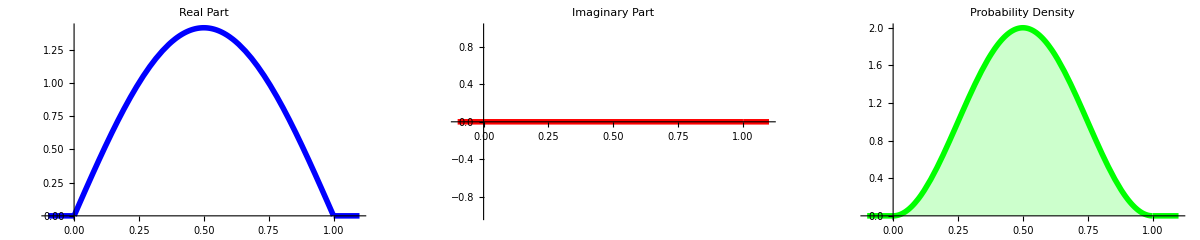

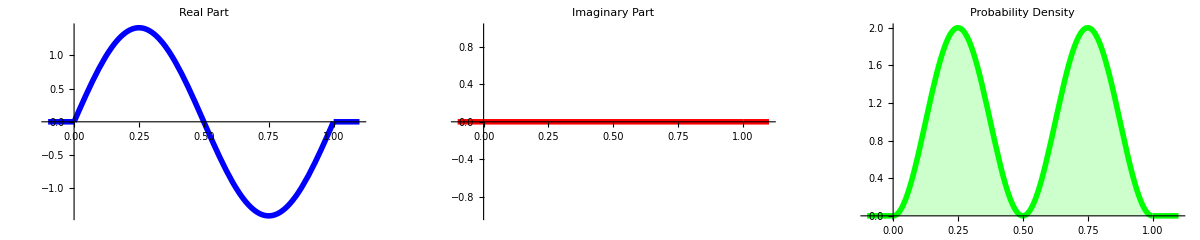

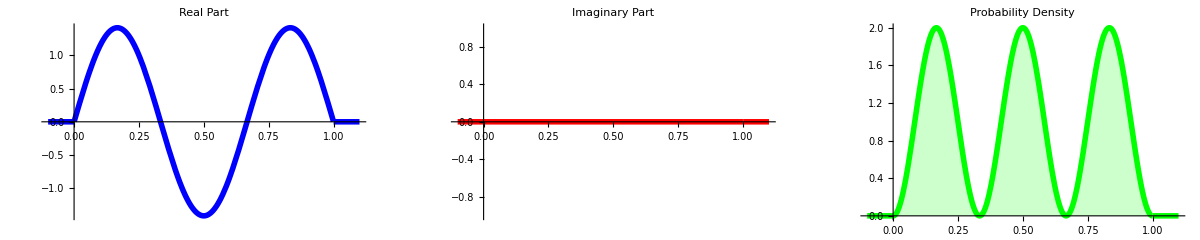

```mathematica
particleInBox[n_, L_] := Function[x, 
  If[0 <= x <= L, 
     Sqrt[2/L] * Sin[n*Pi*x/L], 
     0]
];

(* Plot the first three energy eigenstates *)
psi1Box = particleInBox[1, 1];
psi2Box = particleInBox[2, 1];
psi3Box = particleInBox[3, 1];

plotWaveFunction[psi1Box, {-0.1, 1.1}, "Ground State (n=1) for Particle in a Box"]
plotWaveFunction[psi2Box, {-0.1, 1.1}, "First Excited State (n=2) for Particle in a Box"]
plotWaveFunction[psi3Box, {-0.1, 1.1}, "Second Excited State (n=3) for Particle in a Box"]
```

### Harmonic oscillator wave functions

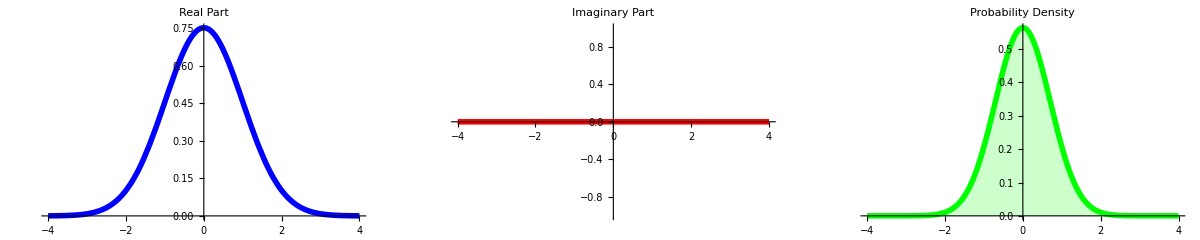

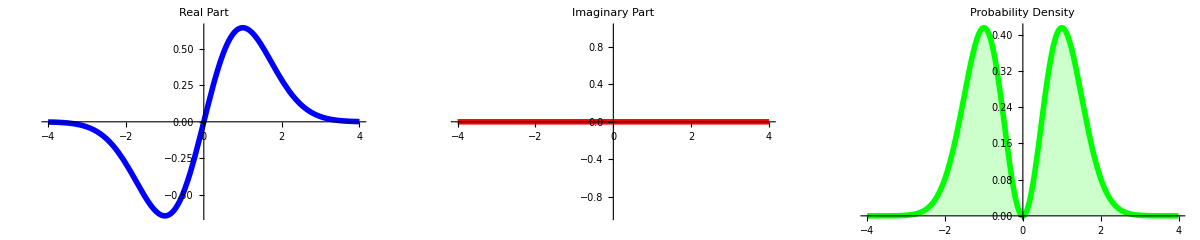

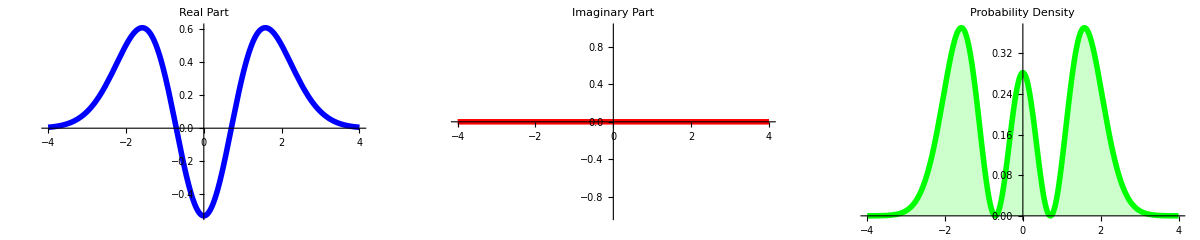

```mathematica
harmonicOscillator[n_, a_] := Function[x, 
  Module[{herm, norm, psi},
    herm = HermiteH[n, x/a];
    norm = 1/Sqrt[2^n * Factorial[n] * Sqrt[Pi] * a];
    psi = norm * herm * Exp[-x^2/(2*a^2)];
    psi
  ]
];

(* Plot the first three energy eigenstates *)
psi0HO = harmonicOscillator[0, 1];
psi1HO = harmonicOscillator[1, 1];
psi2HO = harmonicOscillator[2, 1];

plotWaveFunction[psi0HO, {-4, 4}, "Ground State (n=0) for Harmonic Oscillator"]
plotWaveFunction[psi1HO, {-4, 4}, "First Excited State (n=1) for Harmonic Oscillator"]
plotWaveFunction[psi2HO, {-4, 4}, "Second Excited State (n=2) for Harmonic Oscillator"]
```

### Gaussian Wave Packet (Representing a Free Particle with Momentum)

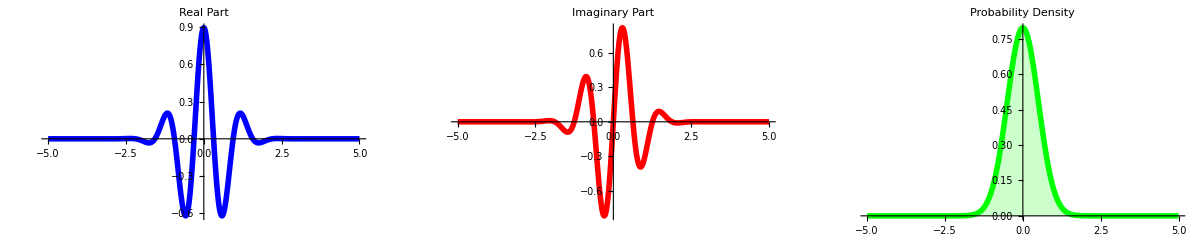

```mathematica
gaussianWavePacket[x0_, p0_, sigma_] := Function[x, 
  (2*Pi*sigma^2)^(-1/4) * Exp[-(x - x0)^2/(4*sigma^2) + I*p0*x]
];

(* Plot a Gaussian wave packet *)
psiGaussian = gaussianWavePacket[0, 5, 0.5];
plotWaveFunction[psiGaussian, {-5, 5}, "Gaussian Wave Packet"]
```

## Linear Operators and Observables

In quantum mechanics, physical observables (measurable quantities) are represented by linear operators acting on the Hilbert space.

Key properties of quantum operators:
1. Hermitian operators represent observables (energy, position, momentum, etc.)
2. Eigenvalues of operators represent the possible measurement outcomes
3. Eigenstates represent the states the system collapses to after measurement

Common operators:
- Position operator: x̂ (multiplication by x in position space)
- Momentum operator: p̂ = -iℏ∂/∂x (differentiation in position space)
- Hamiltonian operator: Ĥ = p̂.b2/2m + V(x̂) (energy)

Operators can be represented as matrices in a discrete basis, or as differential operators in continuous spaces.

```mathematica
(* Demonstration of operators in quantum mechanics *)

(* Define Pauli matrices - the fundamental operators for spin-1/2 systems *)
pauliX = {{0, 1}, {1, 0}};
pauliY = {{0, -I}, {I, 0}};
pauliZ = {{1, 0}, {0, -1}};
identity = {{1, 0}, {0, 1}};

(* Define some common states *)
upState = {1, 0};  (* |0⟩ or |↑⟩ *)
downState = {0, 1};  (* |1⟩ or |↓⟩ *)
plusState = 1/Sqrt[2] {1, 1};  (* |+⟩ *)
minusState = 1/Sqrt[2] {1, -1};  (* |-⟩ *)

(* Demonstrate operator actions *)
Print["X|↑⟩ = ", pauliX.upState, " (flips to |↓⟩)"]
Print["Z|+⟩ = ", pauliZ.plusState, " (phase flip)"]

(* Show expectation values *)
expectationValue[op_, state_] := Conjugate[state].op.state

Print["⟨↑|Z|↑⟩ = ", expectationValue[pauliZ, upState], " (spin up along z-axis)"]
Print["⟨+|Z|+⟩ = ", expectationValue[pauliZ, plusState], " (no preferred direction)"]
Print["⟨+|X|+⟩ = ", expectationValue[pauliX, plusState], " (spin up along x-axis)"]

(* Demonstrate uncertainty principle with position and momentum *)
(* For a Gaussian state, we can calculate the product of uncertainties *)
sigma_x = 1;  (* width of Gaussian in position space *)
sigma_p = 1/(2*sigma_x);  (* width in momentum space from uncertainty principle *)

Print["Δx·Δp = ", sigma_x * sigma_p, " ≥ ℏ/2 = ", 1/2]

(* Visualize the action of operators *)
spinStates = {upState, downState, plusState, minusState};
stateLabels = {"|↑⟩", "|↓⟩", "|+⟩", "|-⟩"};
operators = {pauliX, pauliY, pauliZ, identity};
operatorLabels = {"X", "Y", "Z", "I"};

(* Create a table showing the results of applying each operator to each state *)
resultTable = Table[
  operators[[i]].spinStates[[j]], 
  {i, 1, Length[operators]}, 
  {j, 1, Length[spinStates]}
];

(* Format the complex vectors nicely *)
formatVector[v_] := Module[{s},
  s = ToString[N[v, 3], InputForm];
  s = StringReplace[s, {"List" -> "", "{" -> "{", "}" -> "}", 
                          "I" -> "i", "*^" -> "×10^"}];
  s
]

Grid[
  Prepend[
    Table[
      Prepend[
        Table[formatVector[resultTable[[i, j]]], {j, 1, Length[spinStates]}],
        operatorLabels[[i]]
      ],
      {i, 1, Length[operators]}
    ],
    Prepend[stateLabels, ""]
  ],
  Frame -> All,
  Background -> {None, {LightOrange}}
]

(* Visualize how the Pauli X operator flips states on the Bloch sphere *)
manipulateX = Manipulate[
  Module[{initialState, finalState, blochInitial, blochFinal, t},
    initialState = upState;
    t = θ/Pi;  (* Parameterize from 0 to 1 *)
    finalState = Cos[θ/2]*upState + Sin[θ/2]*downState;
    
    blochInitial = BlochSphereRepresentation[initialState];
    blochFinal = BlochSphereRepresentation[finalState];
    
    Graphics3D[{
      {Opacity[0.2], Sphere[]},
      {Gray, Tube[{{0, 0, -1.2}, {0, 0, 1.2}}, 0.01]},  (* Z-axis *)
      {Gray, Tube[{{-1.2, 0, 0}, {1.2, 0, 0}}, 0.01]},  (* X-axis *)
      {Gray, Tube[{{0, -1.2, 0}, {0, 1.2, 0}}, 0.01]},  (* Y-axis *)
      {Blue, Arrow[{{0, 0, 0}, blochFinal}]},
      {Blue, PointSize[0.02], Point[blochFinal]},
      {Blue, Arrowheads[0.05], Arrow[{{0, 0, 0}, blochInitial}], Text["|↑⟩", 1.1*blochInitial]},
      Text["X rotation = " <> ToString[N[θ/Degree]] <> "°", {0, 0, 1.3}]
    },
    Boxed -> False,
    PlotRange -> 1.3,
    ViewPoint -> {2.5, -1.5, 1.5}]
  ],
  {{θ, 0, "Rotation angle"}, 0, Pi, Pi/20, Appearance -> "Labeled"}
];

manipulateX
```

X|↑⟩ = {0,1} (flips to |↓⟩)

Z|+⟩ = {1/(√2),-1/(√2)} (phase flip)

⟨↑|Z|↑⟩ = 1 (spin up along z-axis)

⟨+|Z|+⟩ = 0 (no preferred direction)

⟨+|X|+⟩ = 1 (spin up along x-axis)

Rule::rhs: Pattern sigma_x appears on the right-hand side of rule sigma_p→1/(2 sigma_x).

Δx·Δp = sigma_p sigma_x ≥ ℏ/2 = 1/2

| |↑⟩ | |↓⟩ | |+⟩ | |-⟩
X | {0, 1.`3.} | {1.`3., 0} | {0.7071067811865474617`3., 0.7071067811865474617`3.} | {-0.7071067811865474617`3., 0.7071067811865474617`3.}
Y | {0, 1.`3.*i} | {-1.`3.*i, 0} | {-0.7071067811865474617`3.*i, 0.7071067811865474617`3.*i} | {0.7071067811865474617`3.*i, 0.7071067811865474617`3.*i}
Z | {1.`3., 0} | {0, -1.`3.} | {0.7071067811865474617`3., -0.7071067811865474617`3.} | {0.7071067811865474617`3., 0.7071067811865474617`3.}
I | {1.`3., 0} | {0, 1.`3.} | {0.7071067811865474617`3., 0.7071067811865474617`3.} | {0.7071067811865474617`3., -0.7071067811865474617`3.}

## Eigenvalues, Eigenstates and Measurement

The measurement process is one of the most distinctive features of quantum mechanics. When we measure an observable:

1. The possible measurement outcomes are the eigenvalues of the corresponding operator
2. The system’s state collapses to the corresponding eigenstate
3. The probability of obtaining a specific eigenvalue is given by |⟨φ|ψ⟩|.b2, where |φ⟩ is the eigenstate

This probabilistic behavior represents a fundamental departure from classical physics. Even with complete knowledge of the state, we can only predict measurement probabilities, not definite outcomes.

After measurement, the system is in an eigenstate of the measured observable. This is known as the “collapse” of the wave function.

Eigenvalues of σx: {-1,1}

Eigenvectors of σx: {{-1,1},{1,1}}

Eigenvalues of σz: {-1,1}

Eigenvectors of σz: {{0,1},{1,0}}

Z-measurement outcomes: {{1,49},{2,51}}

X-measurement outcomes: {{2,100}}

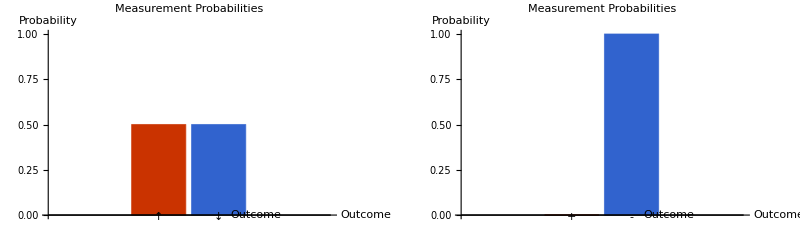

Part::partd: Part specification eigenX⟦1⟧ is longer than depth of object.

Part::partd: Part specification eigenX⟦2⟧ is longer than depth of object.

Part::partd: Part specification eigenX⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

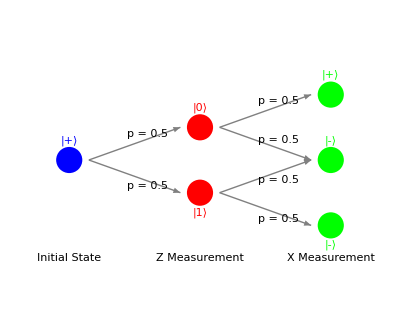

```mathematica
(* Demonstrate measurement and eigenvalues/eigenstates *)

(* Find eigenvalues and eigenvectors of Pauli operators *)
{eigenvaluesX, eigenvectorsX} = Eigensystem[pauliX];
{eigenvaluesZ, eigenvectorsZ} = Eigensystem[pauliZ];

Print["Eigenvalues of σx: ", eigenvaluesX]
Print["Eigenvectors of σx: ", eigenvectorsX]
Print["Eigenvalues of σz: ", eigenvaluesZ]
Print["Eigenvectors of σz: ", eigenvectorsZ]

(* Normalize eigenvectors *)
normalizeVector[v_] := v/Sqrt[v.Conjugate[v]]

eigenX1 = normalizeVector[eigenvectorsX[[1]]];
eigenX2 = normalizeVector[eigenvectorsX[[2]]];
eigenZ1 = normalizeVector[eigenvectorsZ[[1]]];
eigenZ2 = normalizeVector[eigenvectorsZ[[2]]];

(* Simulate a measurement *)
simulateMeasurement[state_, basis_] := Module[
  {probabilities, outcome, i, projector},
  
  (* Calculate probabilities for each basis state *)
  probabilities = Table[
    Abs[Conjugate[basis[[i]]].state]^2,
    {i, 1, Length[basis]}
  ];
  
  (* Choose an outcome based on probabilities *)
  outcome = RandomChoice[probabilities -> Range[Length[basis]]];
  
  (* Return both the outcome and collapsed state *)
  {outcome, basis[[outcome]]}
]

(* Demonstrate measurement on a superposition state *)
superposition = 1/Sqrt[2] {1, 1};  (* |+⟩ state *)

(* Measure in Z basis multiple times *)
measurementResultsZ = Table[
  simulateMeasurement[superposition, {upState, downState}],
  {i, 1, 100}
];

(* Count outcomes *)
outcomeCountsZ = Tally[measurementResultsZ[[All, 1]]];
Print["Z-measurement outcomes: ", outcomeCountsZ]

(* Measure in X basis multiple times *)
measurementResultsX = Table[
  simulateMeasurement[superposition, {eigenX1, eigenX2}],
  {i, 1, 100}
];

(* Count outcomes *)
outcomeCountsX = Tally[measurementResultsX[[All, 1]]];
Print["X-measurement outcomes: ", outcomeCountsX]

(* Visualize measurement probabilities *)
measurementProbs[state_, bases_, labels_] := Module[
  {probs, barChart},
  
  probs = Table[
    Abs[Conjugate[bases[[i]]].state]^2,
    {i, 1, Length[bases]}
  ];
  
  barChart = BarChart[probs, 
    ChartLabels -> labels,
    PlotLabel -> "Measurement Probabilities",
    AxesLabel -> {"Outcome", "Probability"},
    PlotRange -> {0, 1},
    ChartStyle -> ColorData[112],
    ImageSize -> Medium
  ]
]

(* Show measurement probabilities for |+⟩ state in different bases *)
GraphicsRow[{
  measurementProbs[superposition, {upState, downState}, {"↑", "↓"}],
  measurementProbs[superposition, {eigenX1, eigenX2}, {"+", "-"}]
}, ImageSize -> Full]

(* Visualize sequential measurements *)
sequentialMeasurementDemo = Module[
  {initialState, stateAfterZ, possibleOutcomes, stateLabels, measurementSequence},
  
  initialState = 1/Sqrt[2] {1, 1};  (* |+⟩ state *)
  
  (* Possible outcomes of Z measurement *)
  stateAfterZ = {upState, downState};
  possibleOutcomes = {
    {1, stateAfterZ[[1]]}, (* Z measurement gives |0⟩ *)
    {2, stateAfterZ[[2]]}  (* Z measurement gives |1⟩ *)
  };
  
  (* Perform X measurements on each possible outcome *)
  measurementSequence = Table[
    Module[{state = outcome[[2]], xProbs},
      xProbs = Table[Abs[Conjugate[eigenX[[i]]].state]^2, {i, 1, 2}];
      {outcome[[1]], xProbs}
    ],
    {outcome, possibleOutcomes}
  ];
  
  (* Create visualization *)
  stateLabels = {"|0⟩", "|1⟩"};
  
  Graphics[{
    (* Initial state *)
    {Blue, Disk[{0, 0}, 0.2], Text["|+⟩", {0, 0.3}]},
    
    (* Z measurement paths *)
    {Gray, Arrow[{{0.3, 0}, {1.7, 0.5}}]},
    {Gray, Arrow[{{0.3, 0}, {1.7, -0.5}}]},
    
    (* Z measurement outcomes *)
    {Red, Disk[{2, 0.5}, 0.2], Text[stateLabels[[1]], {2, 0.8}]},
    {Red, Disk[{2, -0.5}, 0.2], Text[stateLabels[[2]], {2, -0.8}]},
    
    (* Z measurement probabilities *)
    Text["p = 0.5", {1.2, 0.4}],
    Text["p = 0.5", {1.2, -0.4}],
    
    (* X measurement paths from |0⟩ *)
    {Gray, Arrow[{{2.3, 0.5}, {3.7, 1}}]},
    {Gray, Arrow[{{2.3, 0.5}, {3.7, 0}}]},
    
    (* X measurement paths from |1⟩ *)
    {Gray, Arrow[{{2.3, -0.5}, {3.7, 0}}]},
    {Gray, Arrow[{{2.3, -0.5}, {3.7, -1}}]},
    
    (* X measurement outcomes *)
    {Green, Disk[{4, 1}, 0.2], Text["|+⟩", {4, 1.3}]},
    {Green, Disk[{4, 0}, 0.2], Text["|-⟩", {4, 0.3}]},
    {Green, Disk[{4, -1}, 0.2], Text["|-⟩", {4, -1.3}]},
    
    (* X measurement probabilities *)
    Text["p = 0.5", {3.2, 0.9}],
    Text["p = 0.5", {3.2, 0.3}],
    Text["p = 0.5", {3.2, -0.3}],
    Text["p = 0.5", {3.2, -0.9}],
    
    (* Stages *)
    Text["Initial State", {0, -1.5}],
    Text["Z Measurement", {2, -1.5}],
    Text["X Measurement", {4, -1.5}]
  },
  PlotRange -> {{-0.5, 4.5}, {-2, 2}},
  ImageSize -> Full
  ]
];

sequentialMeasurementDemo
```

## The Schrödinger Equation as the Quantum Equation of Motion

The Schrödinger equation is the fundamental equation governing the time evolution of quantum systems:

iℏ ∂/∂t |ψ(t)⟩ = Ĥ |ψ(t)⟩

where Ĥ is the Hamiltonian operator representing the total energy.

Key properties:
1. The equation is linear, preserving superposition
2. It is first-order in time, making quantum evolution deterministic
3. For time-independent Hamiltonians, the solution is |ψ(t)⟩ = e^(-iĤt/ℏ) |ψ(0)⟩

The time evolution operator U(t) = e^(-iĤt/ℏ) is unitary, preserving normalization and evolving the system in a way that conserves probability.

For stationary states (energy eigenstates), the time evolution is particularly simple:
|ψ(t)⟩ = e^(-iEt/ℏ) |ψ(0)⟩
where the state only acquires a phase factor.

```mathematica
(* Time evolution operator for a given Hamiltonian and time *)
timeEvolutionOperator[hamiltonian_, t_] := MatrixExp[-I * hamiltonian * t];

(* Simple 2-state Hamiltonian (e.g., for a qubit in a magnetic field) *)
H = {{1, 0.5}, {0.5, -1}};

(* Find energy eigenstates *)
{energies, eigenstates} = Eigensystem[H];
Print["Energy eigenvalues: ", energies]

(* Initial state - superposition of energy eigenstates *)
initialState = {1, 0};  (* |0⟩ state *)

(* Decompose initial state in energy basis *)
c1 = Conjugate[eigenstates[[1]]].initialState;
c2 = Conjugate[eigenstates[[2]]].initialState;
Print["Initial state in energy basis: ", c1, " |E₁⟩ + ", c2, " |E₂⟩"]

(* Time evolution of the state *)
evolveState[t_] := timeEvolutionOperator[H, t].initialState

(* Calculate time-dependent expectation values *)
expectationX[t_] := Conjugate[evolveState[t]].pauliX.evolveState[t];
expectationY[t_] := Conjugate[evolveState[t]].pauliY.evolveState[t];
expectationZ[t_] := Conjugate[evolveState[t]].pauliZ.evolveState[t];

(* Plot expectation values over time *)
expectationPlot = Plot[
  {Re[expectationX[t]], Re[expectationY[t]], Re[expectationZ[t]]},
  {t, 0, 10},
  PlotStyle -> {{Red, Thickness[0.01]}, {Green, Thickness[0.01]}, {Blue, Thickness[0.01]}},
  PlotLegends -> {"⟨σₓ⟩", "⟨σᵧ⟩", "⟨σᵣ⟩"},
  AxesLabel -> {"Time", "Expectation Value"},
  PlotLabel -> "Time Evolution of Spin Observables",
  GridLines -> Automatic,
  ImageSize -> Large
];

(* Visualize the time evolution on the Bloch sphere *)
blochEvolution = Manipulate[
  Module[{state, blochVector},
    state = evolveState[t];
    blochVector = {
      Re[Conjugate[state].pauliX.state],
      Re[Conjugate[state].pauliY.state],
      Re[Conjugate[state].pauliZ.state]
    };
    
    Graphics3D[{
      {Opacity[0.2], Sphere[]},
      {Red, Arrowheads[0.05], Arrow[{{0, 0, 0}, {1, 0, 0}}], Text["x", {1.1, 0, 0}]},
      {Green, Arrowheads[0.05], Arrow[{{0, 0, 0}, {0, 1, 0}}], Text["y", {0, 1.1, 0}]},
      {Blue, Arrowheads[0.05], Arrow[{{0, 0, 0}, {0, 0, 1}}], Text["z", {0, 0, 1.1}]},
      {Purple, Thickness[0.01], Line[Table[{
        Re[Conjugate[evolveState[τ]].pauliX.evolveState[τ]],
        Re[Conjugate[evolveState[τ]].pauliY.evolveState[τ]],
        Re[Conjugate[evolveState[τ]].pauliZ.evolveState[τ]]
      }, {τ, 0, t, 0.1}]]},
      {Orange, Arrowheads[0.05], Arrow[{{0, 0, 0}, blochVector}]}
    },
    Boxed -> False,
    PlotRange -> 1.2]
  ],
  {{t, 0, "Time"}, 0, 10, 0.1, Appearance -> "Labeled"}
];

blochEvolution

(* Time evolution of a wave packet *)
(* Parameters *)
x0 = -5;         (* Initial position *)
sigma0 = 1;      (* Initial width *)
k0 = 2;          (* Initial momentum *)
m = 1;           (* Mass *)
hbar = 1;        (* Reduced Planck constant *)

(* Initial Gaussian wave packet *)
initialWavePacket[x_] := (2*Pi*sigma0^2)^(-1/4) * Exp[-(x - x0)^2/(4*sigma0^2) + I*k0*x]

(* Time evolution of free particle wave packet *)
evolvedWavePacket[x_, t_] := Module[
  {sigmat, xt, phase, amplitude},
  
  (* Time-dependent width *)
sigmat = sigma0 * Sqrt[1 + (hbar*t/(2*m*sigma0^2))^2];
  
  (* Center of wave packet *)
  xt = x0 + (hbar*k0/m)*t;
  
  (* Phase factor *)
  phase = (hbar*k0^2/(2*m))*t + 1/2*ArcTan[hbar*t/(2*m*sigma0^2)];
  
  (* Amplitude *)
  amplitude = (2*Pi*sigmat^2)^(-1/4) * Exp[-(x - xt)^2/(4*sigmat^2) + I*k0*x - I*phase];
  
  amplitude
]

(* Visualize the time evolution of a wave packet *)
wavePacketEvolution = Manipulate[
  Module[{psi, realPart, imagPart, probability},
    psi[x_] := evolvedWavePacket[x, t];
    
    realPart = Plot[Re[psi[x]], {x, -10, 10}, 
      PlotStyle -> {Blue, Thickness[0.008]}, 
      PlotRange -> {-0.8, 0.8},
      PlotLabel -> "Real Part"];
      
    imagPart = Plot[Im[psi[x]], {x, -10, 10}, 
      PlotStyle -> {Red, Thickness[0.008]}, 
      PlotRange -> {-0.8, 0.8},
      PlotLabel -> "Imaginary Part"];
      
    probability = Plot[Abs[psi[x]]^2, {x, -10, 10}, 
      PlotStyle -> {Green, Thickness[0.008]}, 
      PlotRange -> {0, 0.8},
      Filling -> Axis, 
      FillingStyle -> Opacity[0.2, Green],
      PlotLabel -> "Probability Density"];
      
    Column[{
      Row[{realPart, imagPart, probability}, Spacer[10]],
      Text[Style["Time: " <> ToString[NumberForm[t, {3, 1}]], Bold, 16]]
    }]
  ],
  {{t, 0, "Time"}, 0, 5, 0.1, Appearance -> "Labeled"},
  SaveDefinitions -> True
]

wavePacketEvolution

(* Demonstrate time evolution for a quantum harmonic oscillator *)
(* Parameters *)
omega = 1;  (* Angular frequency *)

(* Harmonic oscillator energy eigenstates *)
hoEigenstate[n_, x_] := Module[
  {a = Sqrt[m*omega/hbar]},
  1/Sqrt[2^n * Factorial[n]] * (m*omega/Pi/hbar)^(1/4) * 
  Exp[-m*omega*x^2/(2*hbar)] * HermiteH[n, Sqrt[m*omega/hbar]*x]
];

(* Time evolution of energy eigenstate *)
hoTimeEvolution[n_, x_, t_] := 
  hoEigenstate[n, x] * Exp[-I * (n + 1/2) * omega * t];

(* Superposition of states *)
hoSuperposition[x_, t_] := 
  1/Sqrt[2] * hoTimeEvolution[0, x, t] + 
  1/Sqrt[2] * hoTimeEvolution[1, x, t];

(* Visualize harmonic oscillator time evolution *)
hoEvolution = Manipulate[
  Module[{psi, realPart, imagPart, probability, potential},
    psi[x_] := hoSuperposition[x, t];
    
    realPart = Plot[Re[psi[x]], {x, -4, 4}, 
      PlotStyle -> {Blue, Thickness[0.008]}, 
      PlotRange -> {-1.2, 1.2},
      PlotLabel -> "Real Part"];
      
    imagPart = Plot[Im[psi[x]], {x, -4, 4}, 
      PlotStyle -> {Red, Thickness[0.008]}, 
      PlotRange -> {-1.2, 1.2},
      PlotLabel -> "Imaginary Part"];
      
    probability = Plot[{Abs[psi[x]]^2, 0.2*x^2}, {x, -4, 4}, 
      PlotStyle -> {{Green, Thickness[0.008]}, {Black, Dashed}}, 
      PlotRange -> {0, 1.2},
      Filling -> {1 -> Axis}, 
      FillingStyle -> Opacity[0.2, Green],
      PlotLabel -> "Probability Density and Potential",
      PlotLegends -> {"Probability", "Potential (scaled)"}];
      
    Column[{
      Row[{realPart, imagPart, probability}, Spacer[10]],
      Text[Style["Time: " <> ToString[NumberForm[t, {3, 1}]], Bold, 16]],
      Text[Style["Period: T = " <> ToString[NumberForm[2*Pi/omega, {3, 1}]], 14]]
    }]
  ],
  {{t, 0, "Time"}, 0, 2*Pi/omega, Pi/20, Appearance -> "Labeled"},
  SaveDefinitions -> True
];

hoEvolution
```

Energy eigenvalues: {-1.11803,1.11803}

Initial state in energy basis: 0.229753 |E₁⟩ + -0.973249 |E₂⟩

## Conclusion

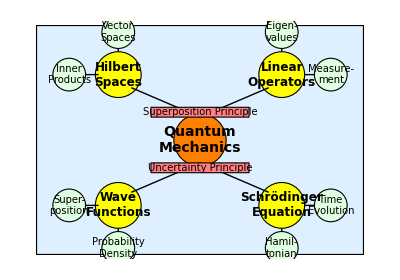

```mathematica
conceptualMap = Graphics[{
  (* Background *)
  {LightBlue, EdgeForm[Black], Rectangle[{0, 0}, {10, 7}]},
  
  (* Central concept *)
  {Orange, EdgeForm[Black], Disk[{5, 3.5}, 0.8]},
  Text[Style["Quantum\nMechanics", Bold, 14], {5, 3.5}],
  
  (* Main branches *)
  {Yellow, EdgeForm[Black], Disk[{2.5, 5.5}, 0.7]},
  Text[Style["Hilbert\nSpaces", Bold, 12], {2.5, 5.5}],
  
  {Yellow, EdgeForm[Black], Disk[{2.5, 1.5}, 0.7]},
  Text[Style["Wave\nFunctions", Bold, 12], {2.5, 1.5}],
  
  {Yellow, EdgeForm[Black], Disk[{7.5, 5.5}, 0.7]},
  Text[Style["Linear\nOperators", Bold, 12], {7.5, 5.5}],
  
  {Yellow, EdgeForm[Black], Disk[{7.5, 1.5}, 0.7]},
  Text[Style["Schrödinger\nEquation", Bold, 12], {7.5, 1.5}],
  
  (* Connecting lines *)
  Line[{{5, 4.2}, {2.9, 5.1}}],
  Line[{{5, 2.8}, {2.9, 1.9}}],
  Line[{{5, 4.2}, {7.1, 5.1}}],
  Line[{{5, 2.8}, {7.1, 1.9}}],
  
  (* Sub-concepts *)
  {LightGreen, EdgeForm[Black], Disk[{1, 5.5}, 0.5]},
  Text[Style["Inner\nProducts", 10], {1, 5.5}],
  Line[{{1.9, 5.5}, {1.5, 5.5}}],
  
  {LightGreen, EdgeForm[Black], Disk[{2.5, 6.8}, 0.5]},
  Text[Style["Vector\nSpaces", 10], {2.5, 6.8}],
  Line[{{2.5, 6.3}, {2.5, 6.2}}],
  
  {LightGreen, EdgeForm[Black], Disk[{1, 1.5}, 0.5]},
  Text[Style["Super-\nposition", 10], {1, 1.5}],
  Line[{{1.9, 1.5}, {1.5, 1.5}}],
  
  {LightGreen, EdgeForm[Black], Disk[{2.5, 0.2}, 0.5]},
  Text[Style["Probability\nDensity", 10], {2.5, 0.2}],
  Line[{{2.5, 0.7}, {2.5, 0.8}}],
  
  {LightGreen, EdgeForm[Black], Disk[{9, 5.5}, 0.5]},
  Text[Style["Measure-\nment", 10], {9, 5.5}],
  Line[{{8.2, 5.5}, {8.5, 5.5}}],
  
  {LightGreen, EdgeForm[Black], Disk[{7.5, 6.8}, 0.5]},
  Text[Style["Eigen-\nvalues", 10], {7.5, 6.8}],
  Line[{{7.5, 6.3}, {7.5, 6.2}}],
  
  {LightGreen, EdgeForm[Black], Disk[{9, 1.5}, 0.5]},
  Text[Style["Time\nEvolution", 10], {9, 1.5}],
  Line[{{8.2, 1.5}, {8.5, 1.5}}],
  
  {LightGreen, EdgeForm[Black], Disk[{7.5, 0.2}, 0.5]},
  Text[Style["Hamil-\ntonian", 10], {7.5, 0.2}],
  Line[{{7.5, 0.7}, {7.5, 0.8}}],
  
  (* Key principles *)
  {Pink, EdgeForm[Black], Rectangle[{3.5, 2.5}, {6.5, 2.8}]},
  Text[Style["Uncertainty Principle", 10], {5, 2.65}],
  
  {Pink, EdgeForm[Black], Rectangle[{3.5, 4.2}, {6.5, 4.5}]},
  Text[Style["Superposition Principle", 10], {5, 4.35}]
},
PlotRange -> {{0, 10}, {0, 7}},
ImageSize -> Full
];

conceptualMap
```